```mathematica
(* 列出支持的文件类型 *)
$ImportFormats
```

{3DS,7z,ACO,Affymetrix,AgilentMicroarray,AIFF,ApacheLog,ArcGRID,AU,AVI,Base64,BDF,Binary,BioImageFormat,Bit,BMP,BSON,Byte,BYU,BZIP2,CDED,CDF,CDX,CDXML,Character16,Character32,Character8,CIF,CML,Complex128,Complex256,Complex64,CSV,Cube,CUR,DAE,DBF,DICOM,DICOMDIR,DIF,DIMACS,Directory,DOT,DTA,DXF,EDF,EML,EPS,ExpressionJSON,ExpressionML,FASTA,FASTQ,FBX,FCHK,FCS,FITS,FLAC,FLV,GaussianLog,GenBank,GeoJSON,GeoTIFF,GIF,GPX,Graph6,Graphlet,GraphML,GRIB,GTOPO30,GXL,GZIP,HarwellBoeing,HDF,HDF5,HEIF,HIN,HTML,HTTPRequest,HTTPResponse,ICC,ICNS,ICO,ICS,Ini,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,ISO,JavaProperties,JavaScriptExpression,JCAMP-DX,JPEG,JPEG2000,JSON,JSONLD,JVX,KML,LaTeX,LEDA,List,LWO,MAT,MathML,Matroska,MBOX,MCTT,MDB,MESH,MGF,MIDI,MMCIF,MO,MOL,MOL2,MP3,MP4,MPS,MTP,MTX,MX,MXNet,NASACDF,NB,NDK,NetCDF,NEXUS,NOFF,NQuads,NTriples,OBJ,ODS,OFF,Ogg,ONNX,OpenEXR,OWLFunctional,Pajek,PBM,PCAP,PCX,PDB,PDF,PEM,PGM,PHPIni,PLY,PNG,PNM,POR,PPM,PXR,PythonExpression,QuickTime,RAR,Raw,RawBitmap,RawJSON,RDFXML,Real128,Real32,Real64,RIB,RLE,RSS,RTF,SAS7BDAT,SAV,SCT,SDF,SDTS,SDTSDEM,SFF,SHP,SMA,SME,SMILES,SND,SP3,SPARQLQuery,SPARQLResultsJSON,SPARQLResultsXML,SPARQLUpdate,Sparse6,STL,String,SurferGrid,SXC,Table,TAR,TerminatedString,TeX,Text,TGA,TGF,TIFF,TIGER,TLE,TriG,TSV,Turtle,UBJSON,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,USGSDEM,UUE,VCF,VCS,VideoFormat,VTK,WARC,WAV,Wave64,WDX,WebP,WL,WLNet,WMLF,WXF,X3D,XBM,XHTML,XHTMLMathML,XLS,XLSX,XML,XPORT,XYZ,ZIP,ZSTD}

```mathematica
(* 导入内置数据 *)
```

```mathematica
Import["ExampleData/numberdata.csv"]
```

{{1.2,4.5,6.7},{5.4,1.,0.},{0.,2.1,3.1}}

```mathematica
(* 查看可用文件的完整列表 *)
ExampleData[All]
```

Join[{{AerialImage,Earth},{AerialImage,FosterCity},{AerialImage,Oakland},{AerialImage,Oakland2},{AerialImage,Pentagon},{AerialImage,Richmond},{AerialImage,Richmond2},{AerialImage,SanDiego},{AerialImage,SanDiego2},{AerialImage,SanDiego3},{AerialImage,SanDiego4},{AerialImage,SanDiego5},{AerialImage,SanDiego6},{AerialImage,SanDiego7},{AerialImage,SanDiego8},{AerialImage,SanDiego9},{AerialImage,SanDiego10},{AerialImage,SanDiego11},{AerialImage,SanDiego12},{AerialImage,SanDiego13},{AerialImage,SanFrancisco},{AerialImage,SanFrancisco2},{AerialImage,SanFrancisco3},{AerialImage,SanFrancisco4},{AerialImage,SanFrancisco5},{AerialImage,SanFrancisco6},{AerialImage,SanFrancisco7},{AerialImage,SanFrancisco8},{AerialImage,SanFrancisco9},{AerialImage,Shreveport},{AerialImage,Stockton},{AerialImage,Stockton2},{AerialImage,Stockton3},{AerialImage,Stockton4},{AerialImage,Stockton5},{AerialImage,Stockton6},{AerialImage,WashingtonIR},{AerialImage,WoodlandHills}},{{Audio,Apollo11ReturnSafely},{Audio,Apollo11SmallStep},{Audio,BalloonPop},{Audio,Bee},{Audio,Bird},{Audio,BlackcapWarbler},{Audio,Cat},{Audio,Cello},{Audio,CelloScale},{Audio,ChurchBell},{Audio,Clapping},{Audio,CreakyDoor},{Audio,Crowd},{Audio,DogBark},{Audio,Drums},{Audio,FemaleVoice},{Audio,Flute},{Audio,FluteScale},{Audio,FogHorn},{Audio,IRMaesHowe},{Audio,IRRailwayTunnel},{Audio,IRSportsCenter},{Audio,IRStairway},{Audio,IRStAndrewsChurch},{Audio,IRStMarysChurch},{Audio,IRYorkMinsterChurch},{Audio,Laughing},{Audio,MaleVoice},{Audio,NoisyTalk},{Audio,Piano},{Audio,PianoScale},{Audio,PowerSupply},{Audio,Scream},{Audio,SubwayTrain},{Audio,Sword},{Audio,ThaiBells},{Audio,Walking},{Audio,Water},{Audio,Wind}},{{ColorTexture,Amboyna},{ColorTexture,Ash},{ColorTexture,BerriesPattern},{ColorTexture,BurlOak},{ColorTexture,CatFur},{ColorTexture,CheetahFur},{ColorTexture,DelisPattern},{ColorTexture,DiamondsPattern},{ColorTexture,FleurPattern},{ColorTexture,FloralPattern1},{ColorTexture,FloralPattern2},{ColorTexture,FloralPattern3},{ColorTexture,FrogsPattern},{ColorTexture,GiraffeFur},{ColorTexture,GloriesPattern},{ColorTexture,GoldenOak},{ColorTexture,GrayMarble},{ColorTexture,GreenMarble},{ColorTexture,Kingwood},{ColorTexture,Laurel},{ColorTexture,LeavesPattern},{ColorTexture,LightCherry},{ColorTexture,Metal1},{ColorTexture,Metal2},{ColorTexture,Metal3},{ColorTexture,Metal4},{ColorTexture,MultiSpiralsPattern},{ColorTexture,OrangeConcrete},{ColorTexture,PaisleyPattern},{ColorTexture,RedApple},{ColorTexture,Roof},{ColorTexture,ScallopPattern},{ColorTexture,StoneWall},{ColorTexture,TriWeavePattern},{ColorTexture,Vavona},{ColorTexture,VinesPattern},{ColorTexture,WavesPattern},{ColorTexture,WheatPattern},{ColorTexture,WhiteMarble},{ColorTexture,YellowMarble}},{{Dataset,Planets},{Dataset,StatePopulations},{Dataset,Titanic}},{{Geometry3D,BassGuitar},{Geometry3D,Beethoven},{Geometry3D,CastleWall},{Geometry3D,Cone},{Geometry3D,Cow},{Geometry3D,Deimos},{Geometry3D,Galleon},{Geometry3D,HammerheadShark},{Geometry3D,Horse},{Geometry3D,KleinBottle},{Geometry3D,MoebiusStrip},{Geometry3D,Phobos},{Geometry3D,PottedPlant},{Geometry3D,Seashell},{Geometry3D,SedanCar},{Geometry3D,SpaceShuttle},{Geometry3D,StanfordBunny},{Geometry3D,Torus},{Geometry3D,Tree},{Geometry3D,Triceratops},{Geometry3D,Tugboat},{Geometry3D,UtahTeapot},{Geometry3D,UtahVWBug},{Geometry3D,Vase},{Geometry3D,VikingLander},{Geometry3D,Wrench},{Geometry3D,Zeppelin}},{{LinearOptimization,25fv47},{LinearOptimization,80bau3b},{LinearOptimization,adlittle},{LinearOptimization,afiro},{LinearOptimization,agg},{LinearOptimization,agg2},{LinearOptimization,agg3},{LinearOptimization,bandm},{LinearOptimization,beaconfd},{LinearOptimization,bgdbg1},{LinearOptimization,bgetam},{LinearOptimization,bgindy},{LinearOptimization,bgprtr},{LinearOptimization,blend},{LinearOptimization,bnl1},{LinearOptimization,bnl2},{LinearOptimization,boeing1},{LinearOptimization,boeing2},{LinearOptimization,bore3d},{LinearOptimization,box1},{LinearOptimization,brandy},{LinearOptimization,capri},{LinearOptimization,ceria3d},{LinearOptimization,chemcom},{LinearOptimization,cplex1},{LinearOptimization,cplex2},{LinearOptimization,cre-a},{LinearOptimization,cre-b},{LinearOptimization,cre-c},{LinearOptimization,cre-d},{LinearOptimization,cycle},{LinearOptimization,czprob},{LinearOptimization,d2q06c},{LinearOptimization,d6cube},{LinearOptimization,degen2},{LinearOptimization,degen3},{LinearOptimization,dfl001},{LinearOptimization,e226},{LinearOptimization,etamacro},{LinearOptimization,ex72a},{LinearOptimization,ex73a},{LinearOptimization,fffff800},{LinearOptimization,finnis},{LinearOptimization,fit1d},{LinearOptimization,fit1p},{LinearOptimization,fit2d},{LinearOptimization,fit2p},{LinearOptimization,forest6},{LinearOptimization,forplan},{LinearOptimization,galenet},{LinearOptimization,ganges},{LinearOptimization,gfrd-pnc},{LinearOptimization,gosh},{LinearOptimization,gran},{LinearOptimization,greenbea},{LinearOptimization,greenbeb},{LinearOptimization,grow15},{LinearOptimization,grow22},{LinearOptimization,grow7},{LinearOptimization,israel},{LinearOptimization,itest2},{LinearOptimization,itest6},{LinearOptimization,kb2},{LinearOptimization,ken-07},{LinearOptimization,ken-11},{LinearOptimization,ken-13},{LinearOptimization,ken-18},{LinearOptimization,klein1},{LinearOptimization,klein2},{LinearOptimization,klein3},{LinearOptimization,lotfi},{LinearOptimization,maros},{LinearOptimization,maros-r7},{LinearOptimization,modszk1},{LinearOptimization,mondou2},{LinearOptimization,nesm},{LinearOptimization,osa-07},{LinearOptimization,osa-14},{LinearOptimization,osa-30},{LinearOptimization,osa-60},{LinearOptimization,pang},{LinearOptimization,pds-02},{LinearOptimization,pds-06},{LinearOptimization,pds-10},{LinearOptimization,pds-20},{LinearOptimization,perold},{LinearOptimization,pilot},{LinearOptimization,pilot4},{LinearOptimization,pilot4i},{LinearOptimization,pilot87},{LinearOptimization,pilot.ja},{LinearOptimization,pilotnov},{LinearOptimization,pilot.we},{LinearOptimization,qual},{LinearOptimization,reactor},{LinearOptimization,recipe},{LinearOptimization,refinery},{LinearOptimization,sc105},{LinearOptimization,sc205},{LinearOptimization,sc50a},{LinearOptimization,sc50b},{LinearOptimization,scagr25},{LinearOptimization,scagr7},{LinearOptimization,scfxm1},{LinearOptimization,scfxm2},{LinearOptimization,scfxm3},{LinearOptimization,scorpion},{LinearOptimization,scrs8},{LinearOptimization,scsd1},{LinearOptimization,scsd6},{LinearOptimization,scsd8},{LinearOptimization,sctap1},{LinearOptimization,sctap2},{LinearOptimization,sctap3},{LinearOptimization,seba},{LinearOptimization,share1b},{LinearOptimization,share2b},{LinearOptimization,shell},{LinearOptimization,ship04l},{LinearOptimization,ship04s},{LinearOptimization,ship08l},{LinearOptimization,ship08s},{LinearOptimization,ship12l},{LinearOptimization,ship12s},{LinearOptimization,sierra},{LinearOptimization,stair},{LinearOptimization,standata},{LinearOptimization,standgub},{LinearOptimization,standmps},{LinearOptimization,stocfor1},{LinearOptimization,stocfor2},{LinearOptimization,tuff},{LinearOptimization,vol1},{LinearOptimization,vtp.base},{LinearOptimization,wood1p},{LinearOptimization,woodinfe},{LinearOptimization,woodw}},{{LinearProgramming,25fv47},{LinearProgramming,80bau3b},{LinearProgramming,adlittle},{LinearProgramming,afiro},{LinearProgramming,agg},{LinearProgramming,agg2},{LinearProgramming,agg3},{LinearProgramming,bandm},{LinearProgramming,beaconfd},{LinearProgramming,bgdbg1},{LinearProgramming,bgetam},{LinearProgramming,bgindy},{LinearProgramming,bgprtr},{LinearProgramming,blend},{LinearProgramming,bnl1},{LinearProgramming,bnl2},{LinearProgramming,boeing1},{LinearProgramming,boeing2},{LinearProgramming,bore3d},{LinearProgramming,box1},{LinearProgramming,brandy},{LinearProgramming,capri},{LinearProgramming,ceria3d},{LinearProgramming,chemcom},{LinearProgramming,cplex1},{LinearProgramming,cplex2},{LinearProgramming,cre-a},{LinearProgramming,cre-b},{LinearProgramming,cre-c},{LinearProgramming,cre-d},{LinearProgramming,cycle},{LinearProgramming,czprob},{LinearProgramming,d2q06c},{LinearProgramming,d6cube},{LinearProgramming,degen2},{LinearProgramming,degen3},{LinearProgramming,dfl001},{LinearProgramming,e226},{LinearProgramming,etamacro},{LinearProgramming,ex72a},{LinearProgramming,ex73a},{LinearProgramming,fffff800},{LinearProgramming,finnis},{LinearProgramming,fit1d},{LinearProgramming,fit1p},{LinearProgramming,fit2d},{LinearProgramming,fit2p},{LinearProgramming,forest6},{LinearProgramming,forplan},{LinearProgramming,galenet},{LinearProgramming,ganges},{LinearProgramming,gfrd-pnc},{LinearProgramming,gosh},{LinearProgramming,gran},{LinearProgramming,greenbea},{LinearProgramming,greenbeb},{LinearProgramming,grow15},{LinearProgramming,grow22},{LinearProgramming,grow7},{LinearProgramming,israel},{LinearProgramming,itest2},{LinearProgramming,itest6},{LinearProgramming,kb2},{LinearProgramming,ken-07},{LinearProgramming,ken-11},{LinearProgramming,ken-13},{LinearProgramming,ken-18},{LinearProgramming,klein1},{LinearProgramming,klein2},{LinearProgramming,klein3},{LinearProgramming,lotfi},{LinearProgramming,maros},{LinearProgramming,maros-r7},{LinearProgramming,modszk1},{LinearProgramming,mondou2},{LinearProgramming,nesm},{LinearProgramming,osa-07},{LinearProgramming,osa-14},{LinearProgramming,osa-30},{LinearProgramming,osa-60},{LinearProgramming,pang},{LinearProgramming,pds-02},{LinearProgramming,pds-06},{LinearProgramming,pds-10},{LinearProgramming,pds-20},{LinearProgramming,perold},{LinearProgramming,pilot},{LinearProgramming,pilot4},{LinearProgramming,pilot4i},{LinearProgramming,pilot87},{LinearProgramming,pilot.ja},{LinearProgramming,pilotnov},{LinearProgramming,pilot.we},{LinearProgramming,qual},{LinearProgramming,reactor},{LinearProgramming,recipe},{LinearProgramming,refinery},{LinearProgramming,sc105},{LinearProgramming,sc205},{LinearProgramming,sc50a},{LinearProgramming,sc50b},{LinearProgramming,scagr25},{LinearProgramming,scagr7},{LinearProgramming,scfxm1},{LinearProgramming,scfxm2},{LinearProgramming,scfxm3},{LinearProgramming,scorpion},{LinearProgramming,scrs8},{LinearProgramming,scsd1},{LinearProgramming,scsd6},{LinearProgramming,scsd8},{LinearProgramming,sctap1},{LinearProgramming,sctap2},{LinearProgramming,sctap3},{LinearProgramming,seba},{LinearProgramming,share1b},{LinearProgramming,share2b},{LinearProgramming,shell},{LinearProgramming,ship04l},{LinearProgramming,ship04s},{LinearProgramming,ship08l},{LinearProgramming,ship08s},{LinearProgramming,ship12l},{LinearProgramming,ship12s},{LinearProgramming,sierra},{LinearProgramming,stair},{LinearProgramming,standata},{LinearProgramming,standgub},{LinearProgramming,standmps},{LinearProgramming,stocfor1},{LinearProgramming,stocfor2},{LinearProgramming,tuff},{LinearProgramming,vol1},{LinearProgramming,vtp.base},{LinearProgramming,wood1p},{LinearProgramming,woodinfe},{LinearProgramming,woodw}},{{MachineLearning,BostonHomes},{MachineLearning,FisherIris},{MachineLearning,MNIST},{MachineLearning,MovieReview},{MachineLearning,Mushroom},{MachineLearning,Satellite},{MachineLearning,Titanic},{MachineLearning,UCILetter},{MachineLearning,WineQuality}},{{Matrix,1138BUS},{Matrix,494BUS},{Matrix,662BUS},{Matrix,685BUS},{Matrix,ABB313},{Matrix,ACUSIM/Pres_Poisson},{Matrix,ADD20},{Matrix,ADD32},{Matrix,AF23560},{Matrix,Alemdar/Alemdar},{Matrix,AMD/G2_circuit},{Matrix,AMD/G3_circuit},{Matrix,Andrews/Andrews},{Matrix,Andrianov/ex3sta1},{Matrix,Andrianov/fxm3_6},{Matrix,Andrianov/fxm4_6},{Matrix,Andrianov/ins2},{Matrix,Andrianov/lp1},{Matrix,Andrianov/lpl1},{Matrix,Andrianov/mip1},{Matrix,Andrianov/net100},{Matrix,Andrianov/net125},{Matrix,Andrianov/net150},{Matrix,Andrianov/net25},{Matrix,Andrianov/net4-1},{Matrix,Andrianov/net50},{Matrix,Andrianov/net75},{Matrix,Andrianov/pattern1},{Matrix,Andrianov/pf2177},{Matrix,ARC130},{Matrix,ASH219},{Matrix,ASH292},{Matrix,ASH331},{Matrix,ASH608},{Matrix,ASH85},{Matrix,ASH958},{Matrix,ATandT/onetone1},{Matrix,ATandT/onetone2},{Matrix,ATandT/pre2},{Matrix,ATandT/twotone},{Matrix,Averous/epb0},{Matrix,Averous/epb1},{Matrix,Averous/epb2},{Matrix,Averous/epb3},{Matrix,Bai/af23560},{Matrix,Bai/bfwa398},{Matrix,Bai/bfwa62},{Matrix,Bai/bfwa782},{Matrix,Bai/bfwb398},{Matrix,Bai/bfwb62},{Matrix,Bai/bfwb782},{Matrix,Bai/bwm200},{Matrix,Bai/bwm2000},{Matrix,Bai/cdde1},{Matrix,Bai/cdde2},{Matrix,Bai/cdde3},{Matrix,Bai/cdde4},{Matrix,Bai/cdde5},{Matrix,Bai/cdde6},{Matrix,Bai/ck104},{Matrix,Bai/ck400},{Matrix,Bai/ck656},{Matrix,Bai/cryg10000},{Matrix,Bai/cryg2500},{Matrix,Bai/dw1024},{Matrix,Bai/dw2048},{Matrix,Bai/dw256A},{Matrix,Bai/dw256B},{Matrix,Bai/dw4096},{Matrix,Bai/dw8192},{Matrix,Bai/dwa512},{Matrix,Bai/dwb512},{Matrix,Bai/dwg961a},{Matrix,Bai/dwg961b},{Matrix,Bai/lop163},{Matrix,Bai/mhd1280a},{Matrix,Bai/mhd1280b},{Matrix,Bai/mhd3200a},{Matrix,Bai/mhd3200b},{Matrix,Bai/mhd4800a},{Matrix,Bai/mhd4800b},{Matrix,Bai/mhda416},{Matrix,Bai/mhdb416},{Matrix,Bai/odepa400},{Matrix,Bai/odepb400},{Matrix,Bai/olm100},{Matrix,Bai/olm1000},{Matrix,Bai/olm2000},{Matrix,Bai/olm500},{Matrix,Bai/olm5000},{Matrix,Bai/pde225},{Matrix,Bai/pde2961},{Matrix,Bai/pde900},{Matrix,Bai/qc2534},{Matrix,Bai/qc324},{Matrix,Bai/qh1484},{Matrix,Bai/qh768},{Matrix,Bai/qh882},{Matrix,Bai/rbsa480},{Matrix,Bai/rbsb480},{Matrix,Bai/rdb1250},{Matrix,Bai/rdb1250l},{Matrix,Bai/rdb200},{Matrix,Bai/rdb200l},{Matrix,Bai/rdb2048},{Matrix,Bai/rdb2048_noL},{Matrix,Bai/rdb3200l},{Matrix,Bai/rdb450},{Matrix,Bai/rdb450l},{Matrix,Bai/rdb5000},{Matrix,Bai/rdb800l},{Matrix,Bai/rdb968},{Matrix,Bai/rw136},{Matrix,Bai/rw496},{Matrix,Bai/rw5151},{Matrix,Bai/tols1090},{Matrix,Bai/tols2000},{Matrix,Bai/tols340},{Matrix,Bai/tols4000},{Matrix,Bai/tols90},{Matrix,Bai/tub100},{Matrix,Bai/tub1000},{Matrix,Barabasi/NotreDame_actors},{Matrix,Barabasi/NotreDame_www},{Matrix,Barabasi/NotreDame_yeast},{Matrix,Bates/Chem97Zt},{Matrix,Bates/Chem97ZtZ},{Matrix,BCSPWR01},{Matrix,BCSPWR02},{Matrix,BCSPWR03},{Matrix,BCSPWR04},{Matrix,BCSPWR05},{Matrix,BCSPWR06},{Matrix,BCSPWR07},{Matrix,BCSPWR08},{Matrix,BCSPWR09},{Matrix,BCSPWR10},{Matrix,BCSSTK01},{Matrix,BCSSTK02},{Matrix,BCSSTK03},{Matrix,BCSSTK04},{Matrix,BCSSTK05},{Matrix,BCSSTK06},{Matrix,BCSSTK07},{Matrix,BCSSTK08},{Matrix,BCSSTK09},{Matrix,BCSSTK10},{Matrix,BCSSTK11},{Matrix,BCSSTK12},{Matrix,BCSSTK13},{Matrix,BCSSTK14},{Matrix,BCSSTK15},{Matrix,BCSSTK16},{Matrix,BCSSTK17},{Matrix,BCSSTK18},{Matrix,BCSSTK19},{Matrix,BCSSTK20},{Matrix,BCSSTK21},{Matrix,BCSSTK22},{Matrix,BCSSTK23},{Matrix,BCSSTK24},{Matrix,BCSSTK25},{Matrix,BCSSTK26},{Matrix,BCSSTK27},{Matrix,BCSSTK28},{Matrix,BCSSTK29},{Matrix,BCSSTK30},{Matrix,BCSSTK31},{Matrix,BCSSTK32},{Matrix,BCSSTK33},{Matrix,BCSSTM01},{Matrix,BCSSTM02},{Matrix,BCSSTM03},{Matrix,BCSSTM04},{Matrix,BCSSTM05},{Matrix,BCSSTM06},{Matrix,BCSSTM07},{Matrix,BCSSTM08},{Matrix,BCSSTM09},{Matrix,BCSSTM10},{Matrix,BCSSTM11},{Matrix,BCSSTM12},{Matrix,BCSSTM13},{Matrix,BCSSTM19},{Matrix,BCSSTM20},{Matrix,BCSSTM21},{Matrix,BCSSTM22},{Matrix,BCSSTM23},{Matrix,BCSSTM24},{Matrix,BCSSTM25},{Matrix,BCSSTM26},{Matrix,BCSSTM27},{Matrix,BEACXC},{Matrix,BEAFLW},{Matrix,BEAUSE},{Matrix,BFW398A},{Matrix,BFW398B},{Matrix,BFW62A},{Matrix,BFW62B},{Matrix,BFW782A},{Matrix,BFW782B},{Matrix,Bindel/ted_A},{Matrix,Bindel/ted_AB},{Matrix,Bindel/ted_AB_unscaled},{Matrix,Bindel/ted_A_unscaled},{Matrix,Bindel/ted_B},{Matrix,Bindel/ted_B_unscaled},{Matrix,BLCKHOLE},{Matrix,Boeing/bcsstk34},{Matrix,Boeing/bcsstk35},{Matrix,Boeing/bcsstk36},{Matrix,Boeing/bcsstk37},{Matrix,Boeing/bcsstk38},{Matrix,Boeing/bcsstk39},{Matrix,Boeing/bcsstm34},{Matrix,Boeing/bcsstm35},{Matrix,Boeing/bcsstm36},{Matrix,Boeing/bcsstm37},{Matrix,Boeing/bcsstm38},{Matrix,Boeing/bcsstm39},{Matrix,Boeing/crystk01},{Matrix,Boeing/crystk02},{Matrix,Boeing/crystk03},{Matrix,Boeing/crystm01},{Matrix,Boeing/crystm02},{Matrix,Boeing/crystm03},{Matrix,Boeing/ct20stif},{Matrix,Boeing/msc00726},{Matrix,Boeing/msc01050},{Matrix,Boeing/msc01440},{Matrix,Boeing/msc04515},{Matrix,Boeing/msc10848},{Matrix,Boeing/msc23052},{Matrix,Boeing/nasa1824},{Matrix,Boeing/nasa2910},{Matrix,Boeing/nasa4704},{Matrix,Boeing/pcrystk02},{Matrix,Boeing/pcrystk03},{Matrix,Boeing/pct20stif},{Matrix,Boeing/pwtk},{Matrix,Bomhof/circuit_1},{Matrix,Bomhof/circuit_2},{Matrix,Bomhof/circuit_3},{Matrix,Bomhof/circuit_4},{Matrix,Bova/rma10},{Matrix,BP0},{Matrix,BP1000},{Matrix,BP1200},{Matrix,BP1400},{Matrix,BP1600},{Matrix,BP200},{Matrix,BP400},{Matrix,BP600},{Matrix,BP800},{Matrix,Brethour/coater1},{Matrix,Brethour/coater2},{Matrix,Brunetiere/thermal},{Matrix,BWM200},{Matrix,BWM2000},{Matrix,Bydder/mri1},{Matrix,Bydder/mri2},{Matrix,CAN1054},{Matrix,CAN1072},{Matrix,CAN144},{Matrix,CAN161},{Matrix,CAN187},{Matrix,CAN229},{Matrix,CAN24},{Matrix,CAN256},{Matrix,CAN268},{Matrix,CAN292},{Matrix,CAN445},{Matrix,CAN61},{Matrix,CAN62},{Matrix,CAN634},{Matrix,CAN715},{Matrix,CAN73},{Matrix,CAN838},{Matrix,CAN96},{Matrix,Cannizzo/sts4098},{Matrix,CAVITY01},{Matrix,CAVITY02},{Matrix,CAVITY03},{Matrix,CAVITY04},{Matrix,CAVITY05},{Matrix,CAVITY06},{Matrix,CAVITY07},{Matrix,CAVITY08},{Matrix,CAVITY09},{Matrix,CAVITY10},{Matrix,CAVITY11},{Matrix,CAVITY12},{Matrix,CAVITY13},{Matrix,CAVITY14},{Matrix,CAVITY15},{Matrix,CAVITY16},{Matrix,CAVITY17},{Matrix,CAVITY18},{Matrix,CAVITY19},{Matrix,CAVITY20},{Matrix,CAVITY21},{Matrix,CAVITY22},{Matrix,CAVITY23},{Matrix,CAVITY24},{Matrix,CAVITY25},{Matrix,CAVITY26},{Matrix,CDDE1},{Matrix,CDDE2},{Matrix,CDDE3},{Matrix,CDDE4},{Matrix,CDDE5},{Matrix,CDDE6},{Matrix,CEGB2802},{Matrix,CEGB2919},{Matrix,CEGB3024},{Matrix,CEGB3306},{Matrix,Chen/pkustk01},{Matrix,Chen/pkustk02},{Matrix,Chen/pkustk03},{Matrix,Chen/pkustk04},{Matrix,Chen/pkustk05},{Matrix,Chen/pkustk06},{Matrix,Chen/pkustk07},{Matrix,Chen/pkustk08},{Matrix,Chen/pkustk09},{Matrix,Chen/pkustk10},{Matrix,Chen/pkustk11},{Matrix,Chen/pkustk12},{Matrix,Chen/pkustk13},{Matrix,Chen/pkustk14},{Matrix,CK104},{Matrix,CK400},{Matrix,CK656},{Matrix,CONF5.0-00L4X4-1000},{Matrix,CONF5.0-00L4X4-1400},{Matrix,CONF5.0-00L4X4-1800},{Matrix,CONF5.0-00L4X4-2200},{Matrix,CONF5.0-00L4X4-2600},{Matrix,CONF5.4-00L8X8-0500},{Matrix,CONF5.4-00L8X8-1000},{Matrix,CONF5.4-00L8X8-1500},{Matrix,CONF5.4-00L8X8-2000},{Matrix,CONF6.0-00L4X4-2000},{Matrix,CONF6.0-00L4X4-3000},{Matrix,CONF6.0-00L8X8-2000},{Matrix,CONF6.0-00L8X8-3000},{Matrix,CONF6.0-00L8X8-8000},{Matrix,Cote/mplate},{Matrix,Cote/vibrobox},{Matrix,CRY10000},{Matrix,CRY2500},{Matrix,Cunningham/k3plates},{Matrix,Cunningham/m3plates},{Matrix,Cunningham/qa8fk},{Matrix,Cunningham/qa8fm},{Matrix,CURTIS54},{Matrix,Cylshell/s1rmq4m1},{Matrix,Cylshell/s1rmt3m1},{Matrix,Cylshell/s2rmq4m1},{Matrix,Cylshell/s2rmt3m1},{Matrix,Cylshell/s3rmq4m1},{Matrix,Cylshell/s3rmt3m1},{Matrix,Cylshell/s3rmt3m3},{Matrix,DNVS/crplat2},{Matrix,DNVS/fcondp2},{Matrix,DNVS/fullb},{Matrix,DNVS/halfb},{Matrix,DNVS/m_t1},{Matrix,DNVS/ship_001},{Matrix,DNVS/ship_003},{Matrix,DNVS/shipsec1},{Matrix,DNVS/shipsec5},{Matrix,DNVS/shipsec8},{Matrix,DNVS/thread},{Matrix,DNVS/trdheim},{Matrix,DNVS/troll},{Matrix,DNVS/tsyl201},{Matrix,DNVS/x104},{Matrix,DRIVCAV/cavity01},{Matrix,DRIVCAV/cavity02},{Matrix,DRIVCAV/cavity03},{Matrix,DRIVCAV/cavity04},{Matrix,DRIVCAV/cavity05},{Matrix,DRIVCAV/cavity06},{Matrix,DRIVCAV/cavity07},{Matrix,DRIVCAV/cavity08},{Matrix,DRIVCAV/cavity09},{Matrix,DRIVCAV/cavity10},{Matrix,DRIVCAV/cavity11},{Matrix,DRIVCAV/cavity12},{Matrix,DRIVCAV/cavity13},{Matrix,DRIVCAV/cavity14},{Matrix,DRIVCAV/cavity15},{Matrix,DRIVCAV/cavity16},{Matrix,DRIVCAV/cavity17},{Matrix,DRIVCAV/cavity18},{Matrix,DRIVCAV/cavity19},{Matrix,DRIVCAV/cavity20},{Matrix,DRIVCAV/cavity21},{Matrix,DRIVCAV/cavity22},{Matrix,DRIVCAV/cavity23},{Matrix,DRIVCAV/cavity24},{Matrix,DRIVCAV/cavity25},{Matrix,DRIVCAV/cavity26},{Matrix,DW2048},{Matrix,DW8192},{Matrix,DWA512},{Matrix,DWB512},{Matrix,DWG961A},{Matrix,DWG961B},{Matrix,DWT1005},{Matrix,DWT1007},{Matrix,DWT1242},{Matrix,DWT162},{Matrix,DWT193},{Matrix,DWT198},{Matrix,DWT209},{Matrix,DWT221},{Matrix,DWT234},{Matrix,DWT245},{Matrix,DWT2680},{Matrix,DWT307},{Matrix,DWT310},{Matrix,DWT346},{Matrix,DWT361},{Matrix,DWT419},{Matrix,DWT492},{Matrix,DWT503},{Matrix,DWT512},{Matrix,DWT59},{Matrix,DWT592},{Matrix,DWT607},{Matrix,DWT66},{Matrix,DWT72},{Matrix,DWT758},{Matrix,DWT869},{Matrix,DWT87},{Matrix,DWT878},{Matrix,DWT918},{Matrix,DWT992},{Matrix,E05R0000},{Matrix,E05R0100},{Matrix,E05R0200},{Matrix,E05R0300},{Matrix,E05R0400},{Matrix,E05R0500},{Matrix,E20R0000},{Matrix,E20R0100},{Matrix,E20R0500},{Matrix,E20R1000},{Matrix,E20R2000},{Matrix,E20R3000},{Matrix,E20R4000},{Matrix,E20R5000},{Matrix,E30R0000},{Matrix,E30R0100},{Matrix,E30R0500},{Matrix,E30R1000},{Matrix,E30R2000},{Matrix,E30R3000},{Matrix,E30R4000},{Matrix,E30R5000},{Matrix,E40R0000},{Matrix,E40R0100},{Matrix,E40R0500},{Matrix,E40R1000},{Matrix,E40R2000},{Matrix,E40R3000},{Matrix,E40R4000},{Matrix,E40R5000},{Matrix,Engwirda/airfoil_2d},{Matrix,ERIS1176},{Matrix,FEMLAB/ns3Da},{Matrix,FEMLAB/poisson2D},{Matrix,FEMLAB/poisson3Da},{Matrix,FEMLAB/poisson3Db},{Matrix,FEMLAB/problem1},{Matrix,FEMLAB/sme3Da},{Matrix,FEMLAB/sme3Db},{Matrix,FEMLAB/sme3Dc},{Matrix,FEMLAB/waveguide3D},{Matrix,FIDAP001},{Matrix,FIDAP002},{Matrix,FIDAP003},{Matrix,FIDAP004},{Matrix,FIDAP005},{Matrix,FIDAP006},{Matrix,FIDAP007},{Matrix,FIDAP008},{Matrix,FIDAP009},{Matrix,FIDAP010},{Matrix,FIDAP011},{Matrix,FIDAP012},{Matrix,FIDAP013},{Matrix,FIDAP014},{Matrix,FIDAP015},{Matrix,FIDAP018},{Matrix,FIDAP019},{Matrix,FIDAP020},{Matrix,FIDAP021},{Matrix,FIDAP022},{Matrix,FIDAP023},{Matrix,FIDAP024},{Matrix,FIDAP025},{Matrix,FIDAP026},{Matrix,FIDAP027},{Matrix,FIDAP028},{Matrix,FIDAP029},{Matrix,FIDAP031},{Matrix,FIDAP032},{Matrix,FIDAP033},{Matrix,FIDAP035},{Matrix,FIDAP036},{Matrix,FIDAP037},{Matrix,FIDAP/ex1},{Matrix,FIDAP/ex10},{Matrix,FIDAP/ex10hs},{Matrix,FIDAP/ex11},{Matrix,FIDAP/ex12},{Matrix,FIDAP/ex13},{Matrix,FIDAP/ex14},{Matrix,FIDAP/ex15},{Matrix,FIDAP/ex18},{Matrix,FIDAP/ex19},{Matrix,FIDAP/ex2},{Matrix,FIDAP/ex20},{Matrix,FIDAP/ex21},{Matrix,FIDAP/ex22},{Matrix,FIDAP/ex23},{Matrix,FIDAP/ex24},{Matrix,FIDAP/ex25},{Matrix,FIDAP/ex26},{Matrix,FIDAP/ex27},{Matrix,FIDAP/ex28},{Matrix,FIDAP/ex29},{Matrix,FIDAP/ex3},{Matrix,FIDAP/ex31},{Matrix,FIDAP/ex32},{Matrix,FIDAP/ex33},{Matrix,FIDAP/ex35},{Matrix,FIDAP/ex36},{Matrix,FIDAP/ex37},{Matrix,FIDAP/ex4},{Matrix,FIDAP/ex40},{Matrix,FIDAP/ex5},{Matrix,FIDAP/ex6},{Matrix,FIDAP/ex7},{Matrix,FIDAP/ex8},{Matrix,FIDAP/ex9},{Matrix,FIDAPM02},{Matrix,FIDAPM03},{Matrix,FIDAPM05},{Matrix,FIDAPM07},{Matrix,FIDAPM08},{Matrix,FIDAPM09},{Matrix,FIDAPM10},{Matrix,FIDAPM11},{Matrix,FIDAPM13},{Matrix,FIDAPM15},{Matrix,FIDAPM29},{Matrix,FIDAPM33},{Matrix,FIDAPM37},{Matrix,FS1831},{Matrix,FS1833},{Matrix,FS1834},{Matrix,FS1836},{Matrix,FS5411},{Matrix,FS5412},{Matrix,FS5413},{Matrix,FS5414},{Matrix,FS6801},{Matrix,FS6802},{Matrix,FS6803},{Matrix,FS7601},{Matrix,FS7602},{Matrix,FS7603},{Matrix,Gaertner/big},{Matrix,Gaertner/nopoly},{Matrix,Gaertner/pesa},{Matrix,Garon/garon1},{Matrix,Garon/garon2},{Matrix,GEMAT1},{Matrix,GEMAT11},{Matrix,GEMAT12},{Matrix,GENT113},{Matrix,GHS_indef/a0nsdsil},{Matrix,GHS_indef/a2nnsnsl},{Matrix,GHS_indef/a5esindl},{Matrix,GHS_indef/aug2d},{Matrix,GHS_indef/aug2dc},{Matrix,GHS_indef/aug3d},{Matrix,GHS_indef/aug3dcqp},{Matrix,GHS_indef/blockqp1},{Matrix,GHS_indef/bloweya},{Matrix,GHS_indef/bloweybl},{Matrix,GHS_indef/bloweybq},{Matrix,GHS_indef/bmw3_2},{Matrix,GHS_indef/boyd1},{Matrix,GHS_indef/boyd2},{Matrix,GHS_indef/brainpc2},{Matrix,GHS_indef/bratu3d},{Matrix,GHS_indef/c-55},{Matrix,GHS_indef/c-58},{Matrix,GHS_indef/c-59},{Matrix,GHS_indef/c-62ghs},{Matrix,GHS_indef/c-63},{Matrix,GHS_indef/c-68},{Matrix,GHS_indef/c-69},{Matrix,GHS_indef/c-70},{Matrix,GHS_indef/c-71},{Matrix,GHS_indef/c-72},{Matrix,GHS_indef/cont-201},{Matrix,GHS_indef/cont-300},{Matrix,GHS_indef/copter2},{Matrix,GHS_indef/cvxqp3},{Matrix,GHS_indef/darcy003},{Matrix,GHS_indef/dawson5},{Matrix,GHS_indef/dixmaanl},{Matrix,GHS_indef/d_pretok},{Matrix,GHS_indef/dtoc},{Matrix,GHS_indef/exdata_1},{Matrix,GHS_indef/helm2d03},{Matrix,GHS_indef/helm3d01},{Matrix,GHS_indef/k1_san},{Matrix,GHS_indef/laser},{Matrix,GHS_indef/linverse},{Matrix,GHS_indef/mario001},{Matrix,GHS_indef/mario002},{Matrix,GHS_indef/ncvxbqp1},{Matrix,GHS_indef/ncvxqp1},{Matrix,GHS_indef/ncvxqp3},{Matrix,GHS_indef/ncvxqp5},{Matrix,GHS_indef/ncvxqp7},{Matrix,GHS_indef/ncvxqp9},{Matrix,GHS_indef/olesnik0},{Matrix,GHS_indef/qpband},{Matrix,GHS_indef/sit100},{Matrix,GHS_indef/sparsine},{Matrix,GHS_indef/spmsrtls},{Matrix,GHS_indef/stokes128},{Matrix,GHS_indef/stokes64},{Matrix,GHS_indef/stokes64s},{Matrix,GHS_indef/tuma1},{Matrix,GHS_indef/tuma2},{Matrix,GHS_indef/turon_m},{Matrix,GHS_psdef/apache1},{Matrix,GHS_psdef/apache2},{Matrix,GHS_psdef/audikw_1},{Matrix,GHS_psdef/bmw7st_1},{Matrix,GHS_psdef/bmwcra_1},{Matrix,GHS_psdef/copter1},{Matrix,GHS_psdef/copter2},{Matrix,GHS_psdef/crankseg_1},{Matrix,GHS_psdef/crankseg_2},{Matrix,GHS_psdef/cvxbqp1},{Matrix,GHS_psdef/finance256},{Matrix,GHS_psdef/ford1},{Matrix,GHS_psdef/ford2},{Matrix,GHS_psdef/gridgena},{Matrix,GHS_psdef/hood},{Matrix,GHS_psdef/inline_1},{Matrix,GHS_psdef/jnlbrng1},{Matrix,GHS_psdef/ldoor},{Matrix,GHS_psdef/minsurfo},{Matrix,GHS_psdef/obstclae},{Matrix,GHS_psdef/oilpan},{Matrix,GHS_psdef/opt1},{Matrix,GHS_psdef/pds10},{Matrix,GHS_psdef/pwt},{Matrix,GHS_psdef/ramage02},{Matrix,GHS_psdef/s3dkq4m2},{Matrix,GHS_psdef/s3dkt3m2},{Matrix,GHS_psdef/srb1},{Matrix,GHS_psdef/torsion1},{Matrix,GHS_psdef/vanbody},{Matrix,GHS_psdef/wathen100},{Matrix,GHS_psdef/wathen120},{Matrix,Goodwin/goodwin},{Matrix,Goodwin/rim},{Matrix,GR3030},{Matrix,Graham/graham1},{Matrix,GRE1107},{Matrix,GRE115},{Matrix,GRE185},{Matrix,GRE216A},{Matrix,GRE216B},{Matrix,GRE343},{Matrix,GRE512},{Matrix,Grund/b1_ss},{Matrix,Grund/b2_ss},{Matrix,Grund/bayer01},{Matrix,Grund/bayer02},{Matrix,Grund/bayer03},{Matrix,Grund/bayer04},{Matrix,Grund/bayer05},{Matrix,Grund/bayer06},{Matrix,Grund/bayer07},{Matrix,Grund/bayer08},{Matrix,Grund/bayer09},{Matrix,Grund/bayer10},{Matrix,Grund/b_dyn},{Matrix,Grund/d_dyn},{Matrix,Grund/d_dyn1},{Matrix,Grund/d_ss},{Matrix,Grund/meg1},{Matrix,Grund/meg4},{Matrix,Grund/poli},{Matrix,Grund/poli_large},{Matrix,Gset/G1},{Matrix,Gset/G10},{Matrix,Gset/G11},{Matrix,Gset/G12},{Matrix,Gset/G13},{Matrix,Gset/G14},{Matrix,Gset/G15},{Matrix,Gset/G16},{Matrix,Gset/G17},{Matrix,Gset/G18},{Matrix,Gset/G19},{Matrix,Gset/G2},{Matrix,Gset/G20},{Matrix,Gset/G21},{Matrix,Gset/G22},{Matrix,Gset/G23},{Matrix,Gset/G24},{Matrix,Gset/G25},{Matrix,Gset/G26},{Matrix,Gset/G27},{Matrix,Gset/G28},{Matrix,Gset/G29},{Matrix,Gset/G3},{Matrix,Gset/G30},{Matrix,Gset/G31},{Matrix,Gset/G32},{Matrix,Gset/G33},{Matrix,Gset/G34},{Matrix,Gset/G35},{Matrix,Gset/G36},{Matrix,Gset/G37},{Matrix,Gset/G38},{Matrix,Gset/G39},{Matrix,Gset/G4},{Matrix,Gset/G40},{Matrix,Gset/G41},{Matrix,Gset/G42},{Matrix,Gset/G43},{Matrix,Gset/G44},{Matrix,Gset/G45},{Matrix,Gset/G46},{Matrix,Gset/G47},{Matrix,Gset/G48},{Matrix,Gset/G49},{Matrix,Gset/G5},{Matrix,Gset/G50},{Matrix,Gset/G51},{Matrix,Gset/G52},{Matrix,Gset/G53},{Matrix,Gset/G54},{Matrix,Gset/G55},{Matrix,Gset/G56},{Matrix,Gset/G57},{Matrix,Gset/G58},{Matrix,Gset/G59},{Matrix,Gset/G6},{Matrix,Gset/G60},{Matrix,Gset/G61},{Matrix,Gset/G62},{Matrix,Gset/G63},{Matrix,Gset/G64},{Matrix,Gset/G65},{Matrix,Gset/G66},{Matrix,Gset/G67},{Matrix,Gset/G7},{Matrix,Gset/G8},{Matrix,Gset/G9},{Matrix,Gupta/gupta1},{Matrix,Gupta/gupta2},{Matrix,Gupta/gupta3},{Matrix,Hamm/add20},{Matrix,Hamm/add32},{Matrix,Hamm/bcircuit},{Matrix,Hamm/hcircuit},{Matrix,Hamm/memplus},{Matrix,Hamm/scircuit},{Matrix,Hamrle/Hamrle1},{Matrix,Hamrle/Hamrle2},{Matrix,Hamrle/Hamrle3},{Matrix,HB/1138_bus},{Matrix,HB/494_bus},{Matrix,HB/662_bus},{Matrix,HB/685_bus},{Matrix,HB/abb313},{Matrix,HB/arc130},{Matrix,HB/ash219},{Matrix,HB/ash292},{Matrix,HB/ash331},{Matrix,HB/ash608},{Matrix,HB/ash85},{Matrix,HB/ash958},{Matrix,HB/bcspwr01},{Matrix,HB/bcspwr02},{Matrix,HB/bcspwr03},{Matrix,HB/bcspwr04},{Matrix,HB/bcspwr05},{Matrix,HB/bcspwr06},{Matrix,HB/bcspwr07},{Matrix,HB/bcspwr08},{Matrix,HB/bcspwr09},{Matrix,HB/bcspwr10},{Matrix,HB/bcsstk01},{Matrix,HB/bcsstk02},{Matrix,HB/bcsstk03},{Matrix,HB/bcsstk04},{Matrix,HB/bcsstk05},{Matrix,HB/bcsstk06},{Matrix,HB/bcsstk07},{Matrix,HB/bcsstk08},{Matrix,HB/bcsstk09},{Matrix,HB/bcsstk10},{Matrix,HB/bcsstk11},{Matrix,HB/bcsstk12},{Matrix,HB/bcsstk13},{Matrix,HB/bcsstk14},{Matrix,HB/bcsstk15},{Matrix,HB/bcsstk16},{Matrix,HB/bcsstk17},{Matrix,HB/bcsstk18},{Matrix,HB/bcsstk19},{Matrix,HB/bcsstk20},{Matrix,HB/bcsstk21},{Matrix,HB/bcsstk22},{Matrix,HB/bcsstk23},{Matrix,HB/bcsstk24},{Matrix,HB/bcsstk25},{Matrix,HB/bcsstk26},{Matrix,HB/bcsstk27},{Matrix,HB/bcsstk28},{Matrix,HB/bcsstk29},{Matrix,HB/bcsstk30},{Matrix,HB/bcsstk31},{Matrix,HB/bcsstk32},{Matrix,HB/bcsstk33},{Matrix,HB/bcsstm01},{Matrix,HB/bcsstm02},{Matrix,HB/bcsstm03},{Matrix,HB/bcsstm04},{Matrix,HB/bcsstm05},{Matrix,HB/bcsstm06},{Matrix,HB/bcsstm07},{Matrix,HB/bcsstm08},{Matrix,HB/bcsstm09},{Matrix,HB/bcsstm10},{Matrix,HB/bcsstm11},{Matrix,HB/bcsstm12},{Matrix,HB/bcsstm13},{Matrix,HB/bcsstm19},{Matrix,HB/bcsstm20},{Matrix,HB/bcsstm21},{Matrix,HB/bcsstm22},{Matrix,HB/bcsstm23},{Matrix,HB/bcsstm24},{Matrix,HB/bcsstm25},{Matrix,HB/bcsstm26},{Matrix,HB/bcsstm27},{Matrix,HB/beacxc},{Matrix,HB/beaflw},{Matrix,HB/beause},{Matrix,HB/blckhole},{Matrix,HB/bp_0},{Matrix,HB/bp_1000},{Matrix,HB/bp_1200},{Matrix,HB/bp_1400},{Matrix,HB/bp_1600},{Matrix,HB/bp_200},{Matrix,HB/bp_400},{Matrix,HB/bp_600},{Matrix,HB/bp_800},{Matrix,HB/can_1054},{Matrix,HB/can_1072},{Matrix,HB/can_144},{Matrix,HB/can_161},{Matrix,HB/can_187},{Matrix,HB/can_229},{Matrix,HB/can_24},{Matrix,HB/can_256},{Matrix,HB/can_268},{Matrix,HB/can_292},{Matrix,HB/can_445},{Matrix,HB/can_61},{Matrix,HB/can_62},{Matrix,HB/can_634},{Matrix,HB/can_715},{Matrix,HB/can_73},{Matrix,HB/can_838},{Matrix,HB/can_96},{Matrix,HB/cegb2802},{Matrix,HB/cegb2919},{Matrix,HB/cegb3024},{Matrix,HB/cegb3306},{Matrix,HB/curtis54},{Matrix,HB/dwt_1005},{Matrix,HB/dwt_1007},{Matrix,HB/dwt_1242},{Matrix,HB/dwt_162},{Matrix,HB/dwt_193},{Matrix,HB/dwt_198},{Matrix,HB/dwt_209},{Matrix,HB/dwt_221},{Matrix,HB/dwt_234},{Matrix,HB/dwt_245},{Matrix,HB/dwt_2680},{Matrix,HB/dwt_307},{Matrix,HB/dwt_310},{Matrix,HB/dwt_346},{Matrix,HB/dwt_361},{Matrix,HB/dwt_419},{Matrix,HB/dwt_492},{Matrix,HB/dwt_503},{Matrix,HB/dwt_512},{Matrix,HB/dwt_59},{Matrix,HB/dwt_592},{Matrix,HB/dwt_607},{Matrix,HB/dwt_66},{Matrix,HB/dwt_72},{Matrix,HB/dwt_758},{Matrix,HB/dwt_869},{Matrix,HB/dwt_87},{Matrix,HB/dwt_878},{Matrix,HB/dwt_918},{Matrix,HB/dwt_992},{Matrix,HB/eris1176},{Matrix,HB/fs_183_1},{Matrix,HB/fs_183_3},{Matrix,HB/fs_183_4},{Matrix,HB/fs_183_6},{Matrix,HB/fs_541_1},{Matrix,HB/fs_541_2},{Matrix,HB/fs_541_3},{Matrix,HB/fs_541_4},{Matrix,HB/fs_680_1},{Matrix,HB/fs_680_2},{Matrix,HB/fs_680_3},{Matrix,HB/fs_760_1},{Matrix,HB/fs_760_2},{Matrix,HB/fs_760_3},{Matrix,HB/gemat1},{Matrix,HB/gemat11},{Matrix,HB/gemat12},{Matrix,HB/gent113},{Matrix,HB/gr_30_30},{Matrix,HB/gre_1107},{Matrix,HB/gre_115},{Matrix,HB/gre_185},{Matrix,HB/gre_216a},{Matrix,HB/gre_216b},{Matrix,HB/gre_343},{Matrix,HB/gre_512},{Matrix,HB/hor_131},{Matrix,HB/ibm32},{Matrix,HB/illc1033},{Matrix,HB/illc1850},{Matrix,HB/impcol_a},{Matrix,HB/impcol_b},{Matrix,HB/impcol_c},{Matrix,HB/impcol_d},{Matrix,HB/impcol_e},{Matrix,HB/jagmesh1},{Matrix,HB/jagmesh2},{Matrix,HB/jagmesh3},{Matrix,HB/jagmesh4},{Matrix,HB/jagmesh5},{Matrix,HB/jagmesh6},{Matrix,HB/jagmesh7},{Matrix,HB/jagmesh8},{Matrix,HB/jagmesh9},{Matrix,HB/jgl009},{Matrix,HB/jgl011},{Matrix,HB/jpwh_991},{Matrix,HB/lap_25},{Matrix,HB/lns_131},{Matrix,HB/lns_3937},{Matrix,HB/lns_511},{Matrix,HB/lnsp_131},{Matrix,HB/lnsp3937},{Matrix,HB/lnsp_511},{Matrix,HB/lock1074},{Matrix,HB/lock2232},{Matrix,HB/lock3491},{Matrix,HB/lock_700},{Matrix,HB/lshp1009},{Matrix,HB/lshp1270},{Matrix,HB/lshp1561},{Matrix,HB/lshp1882},{Matrix,HB/lshp2233},{Matrix,HB/lshp2614},{Matrix,HB/lshp_265},{Matrix,HB/lshp3025},{Matrix,HB/lshp3466},{Matrix,HB/lshp_406},{Matrix,HB/lshp_577},{Matrix,HB/lshp_778},{Matrix,HB/lund_a},{Matrix,HB/lund_b},{Matrix,HB/mahindas},{Matrix,HB/man_5976},{Matrix,HB/mbeacxc},{Matrix,HB/mbeaflw},{Matrix,HB/mbeause},{Matrix,HB/mcca},{Matrix,HB/mcfe},{Matrix,HB/nnc1374},{Matrix,HB/nnc261},{Matrix,HB/nnc666},{Matrix,HB/nos1},{Matrix,HB/nos2},{Matrix,HB/nos3},{Matrix,HB/nos4},{Matrix,HB/nos5},{Matrix,HB/nos6},{Matrix,HB/nos7},{Matrix,HB/orani678},{Matrix,HB/orsirr_1},{Matrix,HB/orsirr_2},{Matrix,HB/orsreg_1},{Matrix,HB/plat1919},{Matrix,HB/plat362},{Matrix,HB/plsk1919},{Matrix,HB/plskz362},{Matrix,HB/pores_1},{Matrix,HB/pores_2},{Matrix,HB/pores_3},{Matrix,HB/psmigr_1},{Matrix,HB/psmigr_2},{Matrix,HB/psmigr_3},{Matrix,HB/rgg010},{Matrix,HB/saylr1},{Matrix,HB/saylr3},{Matrix,HB/saylr4},{Matrix,HB/sherman1},{Matrix,HB/sherman2},{Matrix,HB/sherman3},{Matrix,HB/sherman4},{Matrix,HB/sherman5},{Matrix,HB/shl_0},{Matrix,HB/shl_200},{Matrix,HB/shl_400},{Matrix,HB/sstmodel},{Matrix,HB/steam1},{Matrix,HB/steam2},{Matrix,HB/steam3},{Matrix,HB/str_0},{Matrix,HB/str_200},{Matrix,HB/str_400},{Matrix,HB/str_600},{Matrix,HB/watt_1},{Matrix,HB/watt_2},{Matrix,HB/well1033},{Matrix,HB/well1850},{Matrix,HB/west0067},{Matrix,HB/west0132},{Matrix,HB/west0156},{Matrix,HB/west0167},{Matrix,HB/west0381},{Matrix,HB/west0479},{Matrix,HB/west0497},{Matrix,HB/west0655},{Matrix,HB/west0989},{Matrix,HB/west1505},{Matrix,HB/west2021},{Matrix,HB/will199},{Matrix,HB/will57},{Matrix,HB/wm1},{Matrix,HB/wm2},{Matrix,HB/wm3},{Matrix,HB/young1c},{Matrix,HB/young2c},{Matrix,HB/young3c},{Matrix,HB/young4c},{Matrix,HB/zenios},{Matrix,Hohn/fd12},{Matrix,Hohn/fd15},{Matrix,Hohn/fd18},{Matrix,Hohn/sinc12},{Matrix,Hohn/sinc15},{Matrix,Hohn/sinc18},{Matrix,Hollinger/g7jac010},{Matrix,Hollinger/g7jac010sc},{Matrix,Hollinger/g7jac020},{Matrix,Hollinger/g7jac020sc},{Matrix,Hollinger/g7jac040},{Matrix,Hollinger/g7jac040sc},{Matrix,Hollinger/g7jac050sc},{Matrix,Hollinger/g7jac060},{Matrix,Hollinger/g7jac060sc},{Matrix,Hollinger/g7jac080},{Matrix,Hollinger/g7jac080sc},{Matrix,Hollinger/g7jac100},{Matrix,Hollinger/g7jac100sc},{Matrix,Hollinger/g7jac120},{Matrix,Hollinger/g7jac120sc},{Matrix,Hollinger/g7jac140},{Matrix,Hollinger/g7jac140sc},{Matrix,Hollinger/g7jac160},{Matrix,Hollinger/g7jac160sc},{Matrix,Hollinger/g7jac180},{Matrix,Hollinger/g7jac180sc},{Matrix,Hollinger/g7jac200},{Matrix,Hollinger/g7jac200sc},{Matrix,Hollinger/jan99jac020},{Matrix,Hollinger/jan99jac020sc},{Matrix,Hollinger/jan99jac040},{Matrix,Hollinger/jan99jac040sc},{Matrix,Hollinger/jan99jac060},{Matrix,Hollinger/jan99jac060sc},{Matrix,Hollinger/jan99jac080},{Matrix,Hollinger/jan99jac080sc},{Matrix,Hollinger/jan99jac100},{Matrix,Hollinger/jan99jac100sc},{Matrix,Hollinger/jan99jac120},{Matrix,Hollinger/jan99jac120sc},{Matrix,Hollinger/mark3jac020},{Matrix,Hollinger/mark3jac020sc},{Matrix,Hollinger/mark3jac040},{Matrix,Hollinger/mark3jac040sc},{Matrix,Hollinger/mark3jac060},{Matrix,Hollinger/mark3jac060sc},{Matrix,Hollinger/mark3jac080},{Matrix,Hollinger/mark3jac080sc},{Matrix,Hollinger/mark3jac100},{Matrix,Hollinger/mark3jac100sc},{Matrix,Hollinger/mark3jac120},{Matrix,Hollinger/mark3jac120sc},{Matrix,Hollinger/mark3jac140},{Matrix,Hollinger/mark3jac140sc},{Matrix,HOR131},{Matrix,IBM32},{Matrix,IBM_Austin/coupled},{Matrix,IBM_EDA/ckt11752_dc_1},{Matrix,IBM_EDA/ckt11752_tr_0},{Matrix,IBM_EDA/dc1},{Matrix,IBM_EDA/dc2},{Matrix,IBM_EDA/dc3},{Matrix,IBM_EDA/trans4},{Matrix,IBM_EDA/trans5},{Matrix,ILLC1033},{Matrix,ILLC1850},{Matrix,IMPCOLA},{Matrix,IMPCOLB},{Matrix,IMPCOLC},{Matrix,IMPCOLD},{Matrix,IMPCOLE},{Matrix,INPRO/msdoor},{Matrix,JAGMESH1},{Matrix,JAGMESH2},{Matrix,JAGMESH3},{Matrix,JAGMESH4},{Matrix,JAGMESH5},{Matrix,JAGMESH6},{Matrix,JAGMESH7},{Matrix,JAGMESH8},{Matrix,JAGMESH9},{Matrix,JGL009},{Matrix,JGL011},{Matrix,JPWH991},{Matrix,Kamvar/Stanford},{Matrix,Kamvar/Stanford_Berkeley},{Matrix,Kemelmacher/Kemelmacher},{Matrix,Kim/kim1},{Matrix,Kim/kim2},{Matrix,Koutsovasilis/F1},{Matrix,Langemyr/comsol},{Matrix,LAP25},{Matrix,Li/li},{Matrix,Lin/Lin},{Matrix,Li/pli},{Matrix,LiuWenzhuo/powersim},{Matrix,LNS131},{Matrix,LNS3937},{Matrix,LNS511},{Matrix,LNSP131},{Matrix,LNSP3937},{Matrix,LNSP511},{Matrix,LOCK1074},{Matrix,LOCK2232},{Matrix,LOCK3491},{Matrix,LOCK700},{Matrix,LOP163},{Matrix,Lourakis/bundle1},{Matrix,LPnetlib/lp_25fv47},{Matrix,LPnetlib/lp_80bau3b},{Matrix,LPnetlib/lp_adlittle},{Matrix,LPnetlib/lp_afiro},{Matrix,LPnetlib/lp_agg},{Matrix,LPnetlib/lp_agg2},{Matrix,LPnetlib/lp_agg3},{Matrix,LPnetlib/lp_bandm},{Matrix,LPnetlib/lp_beaconfd},{Matrix,LPnetlib/lp_blend},{Matrix,LPnetlib/lp_bnl1},{Matrix,LPnetlib/lp_bnl2},{Matrix,LPnetlib/lp_bore3d},{Matrix,LPnetlib/lp_brandy},{Matrix,LPnetlib/lp_capri},{Matrix,LPnetlib/lp_cre_a},{Matrix,LPnetlib/lp_cre_b},{Matrix,LPnetlib/lp_cre_c},{Matrix,LPnetlib/lp_cre_d},{Matrix,LPnetlib/lp_cycle},{Matrix,LPnetlib/lp_czprob},{Matrix,LPnetlib/lp_d2q06c},{Matrix,LPnetlib/lp_d6cube},{Matrix,LPnetlib/lp_degen2},{Matrix,LPnetlib/lp_degen3},{Matrix,LPnetlib/lp_dfl001},{Matrix,LPnetlib/lp_e226},{Matrix,LPnetlib/lp_etamacro},{Matrix,LPnetlib/lp_fffff800},{Matrix,LPnetlib/lp_finnis},{Matrix,LPnetlib/lp_fit1d},{Matrix,LPnetlib/lp_fit1p},{Matrix,LPnetlib/lp_fit2d},{Matrix,LPnetlib/lp_fit2p},{Matrix,LPnetlib/lp_ganges},{Matrix,LPnetlib/lp_gfrd_pnc},{Matrix,LPnetlib/lp_greenbea},{Matrix,LPnetlib/lp_greenbeb},{Matrix,LPnetlib/lp_grow15},{Matrix,LPnetlib/lp_grow22},{Matrix,LPnetlib/lp_grow7},{Matrix,LPnetlib/lpi_bgdbg1},{Matrix,LPnetlib/lpi_bgetam},{Matrix,LPnetlib/lpi_bgindy},{Matrix,LPnetlib/lpi_bgprtr},{Matrix,LPnetlib/lpi_box1},{Matrix,LPnetlib/lpi_ceria3d},{Matrix,LPnetlib/lpi_chemcom},{Matrix,LPnetlib/lpi_cplex1},{Matrix,LPnetlib/lpi_cplex2},{Matrix,LPnetlib/lpi_ex72a},{Matrix,LPnetlib/lpi_ex73a},{Matrix,LPnetlib/lpi_forest6},{Matrix,LPnetlib/lpi_galenet},{Matrix,LPnetlib/lpi_gosh},{Matrix,LPnetlib/lpi_gran},{Matrix,LPnetlib/lpi_greenbea},{Matrix,LPnetlib/lpi_itest2},{Matrix,LPnetlib/lpi_itest6},{Matrix,LPnetlib/lpi_klein1},{Matrix,LPnetlib/lpi_klein2},{Matrix,LPnetlib/lpi_klein3},{Matrix,LPnetlib/lpi_mondou2},{Matrix,LPnetlib/lpi_pang},{Matrix,LPnetlib/lpi_pilot4i},{Matrix,LPnetlib/lpi_qual},{Matrix,LPnetlib/lpi_reactor},{Matrix,LPnetlib/lpi_refinery},{Matrix,LPnetlib/lp_israel},{Matrix,LPnetlib/lpi_vol1},{Matrix,LPnetlib/lpi_woodinfe},{Matrix,LPnetlib/lp_kb2},{Matrix,LPnetlib/lp_ken_07},{Matrix,LPnetlib/lp_ken_11},{Matrix,LPnetlib/lp_ken_13},{Matrix,LPnetlib/lp_ken_18},{Matrix,LPnetlib/lp_lotfi},{Matrix,LPnetlib/lp_maros},{Matrix,LPnetlib/lp_maros_r7},{Matrix,LPnetlib/lp_modszk1},{Matrix,LPnetlib/lp_osa_07},{Matrix,LPnetlib/lp_osa_14},{Matrix,LPnetlib/lp_osa_30},{Matrix,LPnetlib/lp_osa_60},{Matrix,LPnetlib/lp_pds_02},{Matrix,LPnetlib/lp_pds_06},{Matrix,LPnetlib/lp_pds_10},{Matrix,LPnetlib/lp_pds_20},{Matrix,LPnetlib/lp_perold},{Matrix,LPnetlib/lp_pilot},{Matrix,LPnetlib/lp_pilot4},{Matrix,LPnetlib/lp_pilot87},{Matrix,LPnetlib/lp_pilot_ja},{Matrix,LPnetlib/lp_pilotnov},{Matrix,LPnetlib/lp_pilot_we},{Matrix,LPnetlib/lp_qap12},{Matrix,LPnetlib/lp_qap15},{Matrix,LPnetlib/lp_qap8},{Matrix,LPnetlib/lp_recipe},{Matrix,LPnetlib/lp_sc105},{Matrix,LPnetlib/lp_sc205},{Matrix,LPnetlib/lp_sc50a},{Matrix,LPnetlib/lp_sc50b},{Matrix,LPnetlib/lp_scagr25},{Matrix,LPnetlib/lp_scagr7},{Matrix,LPnetlib/lp_scfxm1},{Matrix,LPnetlib/lp_scfxm2},{Matrix,LPnetlib/lp_scfxm3},{Matrix,LPnetlib/lp_scorpion},{Matrix,LPnetlib/lp_scrs8},{Matrix,LPnetlib/lp_scsd1},{Matrix,LPnetlib/lp_scsd6},{Matrix,LPnetlib/lp_scsd8},{Matrix,LPnetlib/lp_sctap1},{Matrix,LPnetlib/lp_sctap2},{Matrix,LPnetlib/lp_sctap3},{Matrix,LPnetlib/lp_share1b},{Matrix,LPnetlib/lp_share2b},{Matrix,LPnetlib/lp_shell},{Matrix,LPnetlib/lp_ship04l},{Matrix,LPnetlib/lp_ship04s},{Matrix,LPnetlib/lp_ship08l},{Matrix,LPnetlib/lp_ship08s},{Matrix,LPnetlib/lp_ship12l},{Matrix,LPnetlib/lp_ship12s},{Matrix,LPnetlib/lp_sierra},{Matrix,LPnetlib/lp_stair},{Matrix,LPnetlib/lp_standata},{Matrix,LPnetlib/lp_standgub},{Matrix,LPnetlib/lp_standmps},{Matrix,LPnetlib/lp_stocfor1},{Matrix,LPnetlib/lp_stocfor2},{Matrix,LPnetlib/lp_stocfor3},{Matrix,LPnetlib/lp_truss},{Matrix,LPnetlib/lp_tuff},{Matrix,LPnetlib/lp_vtp_base},{Matrix,LPnetlib/lp_wood1p},{Matrix,LPnetlib/lp_woodw},{Matrix,LSHP1009},{Matrix,LSHP1270},{Matrix,LSHP1561},{Matrix,LSHP1882},{Matrix,LSHP2233},{Matrix,LSHP2614},{Matrix,LSHP265},{Matrix,LSHP3025},{Matrix,LSHP3466},{Matrix,LSHP406},{Matrix,LSHP577},{Matrix,LSHP778},{Matrix,Lucifora/cell1},{Matrix,Lucifora/cell2},{Matrix,LUNDA},{Matrix,LUNDB},{Matrix,MAHINDAS},{Matrix,Mallya/lhr01},{Matrix,Mallya/lhr02},{Matrix,Mallya/lhr04},{Matrix,Mallya/lhr04c},{Matrix,Mallya/lhr07},{Matrix,Mallya/lhr07c},{Matrix,Mallya/lhr10},{Matrix,Mallya/lhr10c},{Matrix,Mallya/lhr11},{Matrix,Mallya/lhr11c},{Matrix,Mallya/lhr14},{Matrix,Mallya/lhr14c},{Matrix,Mallya/lhr17},{Matrix,Mallya/lhr17c},{Matrix,Mallya/lhr34},{Matrix,Mallya/lhr34c},{Matrix,Mallya/lhr71},{Matrix,Mallya/lhr71c},{Matrix,MAN5976},{Matrix,MathWorks/Harvard500},{Matrix,MathWorks/Kaufhold},{Matrix,MathWorks/Kuu},{Matrix,MathWorks/Muu},{Matrix,MathWorks/Pd},{Matrix,MathWorks/Pd_rhs},{Matrix,MathWorks/pivtol},{Matrix,MathWorks/Sieber},{Matrix,MathWorks/tomography},{Matrix,MBEACXC},{Matrix,MBEAFLW},{Matrix,MBEAUSE},{Matrix,MCCA},{Matrix,MCFE},{Matrix,MEMPLUS},{Matrix,Meszaros/aa01},{Matrix,Meszaros/aa03},{Matrix,Meszaros/aa3},{Matrix,Meszaros/aa4},{Matrix,Meszaros/aa5},{Matrix,Meszaros/aa6},{Matrix,Meszaros/air02},{Matrix,Meszaros/air03},{Matrix,Meszaros/air04},{Matrix,Meszaros/air05},{Matrix,Meszaros/air06},{Matrix,Meszaros/aircraft},{Matrix,Meszaros/bas1lp},{Matrix,Meszaros/baxter},{Matrix,Meszaros/car4},{Matrix,Meszaros/cari},{Matrix,Meszaros/cep1},{Matrix,Meszaros/ch},{Matrix,Meszaros/co5},{Matrix,Meszaros/co9},{Matrix,Meszaros/complex},{Matrix,Meszaros/cq5},{Matrix,Meszaros/cq9},{Matrix,Meszaros/cr42},{Matrix,Meszaros/crew1},{Matrix,Meszaros/dano3mip},{Matrix,Meszaros/dbic1},{Matrix,Meszaros/dbir1},{Matrix,Meszaros/dbir2},{Matrix,Meszaros/de063155},{Matrix,Meszaros/de063157},{Matrix,Meszaros/de080285},{Matrix,Meszaros/degme},{Matrix,Meszaros/delf},{Matrix,Meszaros/deter0},{Matrix,Meszaros/deter1},{Matrix,Meszaros/deter2},{Matrix,Meszaros/deter3},{Matrix,Meszaros/deter4},{Matrix,Meszaros/deter5},{Matrix,Meszaros/deter6},{Matrix,Meszaros/deter7},{Matrix,Meszaros/deter8},{Matrix,Meszaros/df2177},{Matrix,Meszaros/e18},{Matrix,Meszaros/ex3sta1},{Matrix,Meszaros/farm},{Matrix,Meszaros/fxm2-16},{Matrix,Meszaros/fxm2-6},{Matrix,Meszaros/fxm3_16},{Matrix,Meszaros/fxm3_6},{Matrix,Meszaros/fxm4_6},{Matrix,Meszaros/gams10a},{Matrix,Meszaros/gams10am},{Matrix,Meszaros/gams30a},{Matrix,Meszaros/gams30am},{Matrix,Meszaros/gams60am},{Matrix,Meszaros/gas11},{Matrix,Meszaros/ge},{Matrix,Meszaros/gen},{Matrix,Meszaros/gen1},{Matrix,Meszaros/gen2},{Matrix,Meszaros/gen4},{Matrix,Meszaros/iiasa},{Matrix,Meszaros/iprob},{Matrix,Meszaros/jendrec1},{Matrix,Meszaros/karted},{Matrix,Meszaros/kl02},{Matrix,Meszaros/kleemin},{Matrix,Meszaros/l30},{Matrix,Meszaros/l9},{Matrix,Meszaros/large},{Matrix,Meszaros/lp22},{Matrix,Meszaros/lpl2},{Matrix,Meszaros/lpl3},{Matrix,Meszaros/mod2},{Matrix,Meszaros/model1},{Matrix,Meszaros/model10},{Matrix,Meszaros/model2},{Matrix,Meszaros/model3},{Matrix,Meszaros/model4},{Matrix,Meszaros/model5},{Matrix,Meszaros/model6},{Matrix,Meszaros/model7},{Matrix,Meszaros/model8},{Matrix,Meszaros/model9},{Matrix,Meszaros/nemsafm},{Matrix,Meszaros/nemscem},{Matrix,Meszaros/nemsemm1},{Matrix,Meszaros/nemsemm2},{Matrix,Meszaros/nemspmm1},{Matrix,Meszaros/nemspmm2},{Matrix,Meszaros/nemswrld},{Matrix,Meszaros/nl},{Matrix,Meszaros/nsct},{Matrix,Meszaros/nsic},{Matrix,Meszaros/nsir},{Matrix,Meszaros/nw14},{Matrix,Meszaros/p0033},{Matrix,Meszaros/p0040},{Matrix,Meszaros/p010},{Matrix,Meszaros/p0201},{Matrix,Meszaros/p0282},{Matrix,Meszaros/p0291},{Matrix,Meszaros/p05},{Matrix,Meszaros/p0548},{Matrix,Meszaros/p2756},{Matrix,Meszaros/p6000},{Matrix,Meszaros/pcb1000},{Matrix,Meszaros/pcb3000},{Matrix,Meszaros/pf2177},{Matrix,Meszaros/pgp2},{Matrix,Meszaros/plddb},{Matrix,Meszaros/pltexpa},{Matrix,Meszaros/primagaz},{Matrix,Meszaros/problem},{Matrix,Meszaros/progas},{Matrix,Meszaros/qiulp},{Matrix,Meszaros/r05},{Matrix,Meszaros/rat},{Matrix,Meszaros/refine},{Matrix,Meszaros/rlfddd},{Matrix,Meszaros/rlfdual},{Matrix,Meszaros/rlfprim},{Matrix,Meszaros/rosen1},{Matrix,Meszaros/rosen10},{Matrix,Meszaros/rosen2},{Matrix,Meszaros/rosen7},{Matrix,Meszaros/rosen8},{Matrix,Meszaros/route},{Matrix,Meszaros/sc205-2r},{Matrix,Meszaros/scagr7-2b},{Matrix,Meszaros/scagr7-2c},{Matrix,Meszaros/scagr7-2r},{Matrix,Meszaros/scfxm1-2b},{Matrix,Meszaros/scfxm1-2r},{Matrix,Meszaros/scrs8-2b},{Matrix,Meszaros/scrs8-2c},{Matrix,Meszaros/scrs8-2r},{Matrix,Meszaros/scsd8-2b},{Matrix,Meszaros/scsd8-2c},{Matrix,Meszaros/scsd8-2r},{Matrix,Meszaros/sctap1-2b},{Matrix,Meszaros/sctap1-2c},{Matrix,Meszaros/sctap1-2r},{Matrix,Meszaros/seymourl},{Matrix,Meszaros/slptsk},{Matrix,Meszaros/small},{Matrix,Meszaros/south31},{Matrix,Meszaros/stat96v1},{Matrix,Meszaros/stat96v2},{Matrix,Meszaros/stat96v3},{Matrix,Meszaros/stat96v4},{Matrix,Meszaros/stat96v5},{Matrix,Meszaros/stoch_aircraft},{Matrix,Meszaros/stormg2-125},{Matrix,Meszaros/stormg2-27},{Matrix,Meszaros/stormg2-8},{Matrix,Meszaros/t0331-4l},{Matrix,Meszaros/testbig},{Matrix,Meszaros/tp-6},{Matrix,Meszaros/ts-palko},{Matrix,Meszaros/ulevimin},{Matrix,Meszaros/us04},{Matrix,Meszaros/world},{Matrix,Meszaros/zed},{Matrix,MHD1280A},{Matrix,MHD1280B},{Matrix,MHD3200A},{Matrix,MHD3200B},{Matrix,MHD416A},{Matrix,MHD416B},{Matrix,MHD4800A},{Matrix,MHD4800B},{Matrix,Mittelmann/cont11_l},{Matrix,Mittelmann/cont1_l},{Matrix,Mittelmann/fome11},{Matrix,Mittelmann/fome12},{Matrix,Mittelmann/fome13},{Matrix,Mittelmann/fome20},{Matrix,Mittelmann/fome21},{Matrix,Mittelmann/neos},{Matrix,Mittelmann/neos1},{Matrix,Mittelmann/neos2},{Matrix,Mittelmann/neos3},{Matrix,Mittelmann/nug08-3rd},{Matrix,Mittelmann/pds-100},{Matrix,Mittelmann/pds-30},{Matrix,Mittelmann/pds-40},{Matrix,Mittelmann/pds-50},{Matrix,Mittelmann/pds-60},{Matrix,Mittelmann/pds-70},{Matrix,Mittelmann/pds-80},{Matrix,Mittelmann/pds-90},{Matrix,Mittelmann/rail2586},{Matrix,Mittelmann/rail4284},{Matrix,Mittelmann/rail507},{Matrix,Mittelmann/rail516},{Matrix,Mittelmann/rail582},{Matrix,Mittelmann/sgpf5y6},{Matrix,Mittelmann/spal_004},{Matrix,Mittelmann/stormG2_1000},{Matrix,Mittelmann/watson_1},{Matrix,Mittelmann/watson_2},{Matrix,MKS/fp},{Matrix,Morandini/robot},{Matrix,Morandini/rotor1},{Matrix,Morandini/rotor2},{Matrix,Mulvey/finan512},{Matrix,Mulvey/pfinan512},{Matrix,Nasa/barth},{Matrix,Nasa/barth4},{Matrix,Nasa/barth5},{Matrix,Nasa/nasa1824},{Matrix,Nasa/nasa2146},{Matrix,Nasa/nasa2910},{Matrix,Nasa/nasa4704},{Matrix,Nasa/nasasrb},{Matrix,Nasa/pwt},{Matrix,Nasa/shuttle_eddy},{Matrix,Nasa/skirt},{Matrix,ND/nd12k},{Matrix,ND/nd24k},{Matrix,ND/nd3k},{Matrix,ND/nd6k},{Matrix,Nemeth/nemeth01},{Matrix,Nemeth/nemeth02},{Matrix,Nemeth/nemeth03},{Matrix,Nemeth/nemeth04},{Matrix,Nemeth/nemeth05},{Matrix,Nemeth/nemeth06},{Matrix,Nemeth/nemeth07},{Matrix,Nemeth/nemeth08},{Matrix,Nemeth/nemeth09},{Matrix,Nemeth/nemeth10},{Matrix,Nemeth/nemeth11},{Matrix,Nemeth/nemeth12},{Matrix,Nemeth/nemeth13},{Matrix,Nemeth/nemeth14},{Matrix,Nemeth/nemeth15},{Matrix,Nemeth/nemeth16},{Matrix,Nemeth/nemeth17},{Matrix,Nemeth/nemeth18},{Matrix,Nemeth/nemeth19},{Matrix,Nemeth/nemeth20},{Matrix,Nemeth/nemeth21},{Matrix,Nemeth/nemeth22},{Matrix,Nemeth/nemeth23},{Matrix,Nemeth/nemeth24},{Matrix,Nemeth/nemeth25},{Matrix,Nemeth/nemeth26},{Matrix,NNC1374},{Matrix,NNC261},{Matrix,NNC666},{Matrix,Norris/fv1},{Matrix,Norris/fv2},{Matrix,Norris/fv3},{Matrix,Norris/heart1},{Matrix,Norris/heart2},{Matrix,Norris/heart3},{Matrix,Norris/lung1},{Matrix,Norris/lung2},{Matrix,Norris/stomach},{Matrix,Norris/torso1},{Matrix,Norris/torso2},{Matrix,Norris/torso3},{Matrix,NOS1},{Matrix,NOS2},{Matrix,NOS3},{Matrix,NOS4},{Matrix,NOS5},{Matrix,NOS6},{Matrix,NOS7},{Matrix,Oberwolfach/bone010},{Matrix,Oberwolfach/boneS01},{Matrix,Oberwolfach/boneS10},{Matrix,Oberwolfach/chipcool0},{Matrix,Oberwolfach/chipcool1},{Matrix,Oberwolfach/filter2D},{Matrix,Oberwolfach/filter3D},{Matrix,Oberwolfach/flowmeter0},{Matrix,Oberwolfach/flowmeter5},{Matrix,Oberwolfach/gas_sensor},{Matrix,Oberwolfach/gyro},{Matrix,Oberwolfach/gyro_k},{Matrix,Oberwolfach/gyro_m},{Matrix,Oberwolfach/inlet},{Matrix,Oberwolfach/LF10},{Matrix,Oberwolfach/LF10000},{Matrix,Oberwolfach/LFAT5},{Matrix,Oberwolfach/LFAT5000},{Matrix,Oberwolfach/piston},{Matrix,Oberwolfach/rail_1357},{Matrix,Oberwolfach/rail_20209},{Matrix,Oberwolfach/rail_5177},{Matrix,Oberwolfach/rail_79841},{Matrix,Oberwolfach/spiral},{Matrix,Oberwolfach/t2dah},{Matrix,Oberwolfach/t2dah_a},{Matrix,Oberwolfach/t2dah_e},{Matrix,Oberwolfach/t2dal},{Matrix,Oberwolfach/t2dal_a},{Matrix,Oberwolfach/t2dal_bci},{Matrix,Oberwolfach/t2dal_e},{Matrix,Oberwolfach/t3dh},{Matrix,Oberwolfach/t3dh_a},{Matrix,Oberwolfach/t3dh_e},{Matrix,Oberwolfach/t3dl},{Matrix,Oberwolfach/t3dl_a},{Matrix,Oberwolfach/t3dl_e},{Matrix,Oberwolfach/windscreen},{Matrix,ODEP400A},{Matrix,ODEP400B},{Matrix,Okunbor/aft01},{Matrix,Okunbor/aft02},{Matrix,OLM100},{Matrix,OLM1000},{Matrix,OLM2000},{Matrix,OLM500},{Matrix,OLM5000},{Matrix,ORANI678},{Matrix,ORSIRR1},{Matrix,ORSIRR2},{Matrix,ORSREG1},{Matrix,Pajek/California},{Matrix,Pajek/Cities},{Matrix,Pajek/CSphd},{Matrix,Pajek/dictionary28},{Matrix,Pajek/divorce},{Matrix,Pajek/EAT_RS},{Matrix,Pajek/EAT_SR},{Matrix,Pajek/EPA},{Matrix,Pajek/Erdos02},{Matrix,Pajek/Erdos971},{Matrix,Pajek/Erdos972},{Matrix,Pajek/Erdos981},{Matrix,Pajek/Erdos982},{Matrix,Pajek/Erdos991},{Matrix,Pajek/Erdos992},{Matrix,Pajek/EVA},{Matrix,Pajek/FA},{Matrix,Pajek/foldoc},{Matrix,Pajek/football},{Matrix,Pajek/GD00_a},{Matrix,Pajek/GD00_c},{Matrix,Pajek/GD01_a},{Matrix,Pajek/GD01_A},{Matrix,Pajek/GD01_b},{Matrix,Pajek/GD01_c},{Matrix,Pajek/GD02_a},{Matrix,Pajek/GD02_b},{Matrix,Pajek/GD06_Java},{Matrix,Pajek/GD06_theory},{Matrix,Pajek/GD95_a},{Matrix,Pajek/GD95_b},{Matrix,Pajek/GD95_c},{Matrix,Pajek/GD96_a},{Matrix,Pajek/GD96_b},{Matrix,Pajek/GD96_c},{Matrix,Pajek/GD96_d},{Matrix,Pajek/GD97_a},{Matrix,Pajek/GD97_b},{Matrix,Pajek/GD97_c},{Matrix,Pajek/GD98_a},{Matrix,Pajek/GD98_b},{Matrix,Pajek/GD98_c},{Matrix,Pajek/GD99_b},{Matrix,Pajek/GD99_c},{Matrix,Pajek/geom},{Matrix,Pajek/GlossGT},{Matrix,Pajek/HEP-th},{Matrix,Pajek/HEP-th-new},{Matrix,Pajek/IMDB},{Matrix,Pajek/internet},{Matrix,Pajek/Journals},{Matrix,Pajek/Kohonen},{Matrix,Pajek/Lederberg},{Matrix,Pajek/ODLIS},{Matrix,Pajek/patents},{Matrix,Pajek/patents_main},{Matrix,Pajek/Ragusa16},{Matrix,Pajek/Ragusa18},{Matrix,Pajek/Reuters911},{Matrix,Pajek/Roget},{Matrix,Pajek/Sandi_authors},{Matrix,Pajek/Sandi_sandi},{Matrix,Pajek/SciMet},{Matrix,Pajek/SmaGri},{Matrix,Pajek/SmallW},{Matrix,Pajek/Stranke94},{Matrix,Pajek/Tina_AskCal},{Matrix,Pajek/Tina_AskCog},{Matrix,Pajek/Tina_DisCal},{Matrix,Pajek/Tina_DisCog},{Matrix,Pajek/USAir97},{Matrix,Pajek/USpowerGrid},{Matrix,Pajek/Wordnet3},{Matrix,Pajek/WorldCities},{Matrix,Pajek/yeast},{Matrix,Pajek/Zewail},{Matrix,PARSEC/benzene},{Matrix,PARSEC/CO},{Matrix,PARSEC/Ga10As10H30},{Matrix,PARSEC/Ga19As19H42},{Matrix,PARSEC/Ga3As3H12},{Matrix,PARSEC/Ga41As41H72},{Matrix,PARSEC/GaAsH6},{Matrix,PARSEC/Ge87H76},{Matrix,PARSEC/Ge99H100},{Matrix,PARSEC/H2O},{Matrix,PARSEC/Na5},{Matrix,PARSEC/Si10H16},{Matrix,PARSEC/Si2},{Matrix,PARSEC/Si34H36},{Matrix,PARSEC/Si41Ge41H72},{Matrix,PARSEC/Si5H12},{Matrix,PARSEC/Si87H76},{Matrix,PARSEC/SiH4},{Matrix,PARSEC/SiNa},{Matrix,PARSEC/SiO},{Matrix,PARSEC/SiO2},{Matrix,PDE225},{Matrix,PDE2961},{Matrix,PDE900},{Matrix,Pereyra/landmark},{Matrix,PLAT1919},{Matrix,PLAT362},{Matrix,PLSK1919},{Matrix,PLSKZ362},{Matrix,POLYFLOW/invextr1_new},{Matrix,POLYFLOW/mixtank_new},{Matrix,PORES1},{Matrix,PORES2},{Matrix,PORES3},{Matrix,Pothen/barth},{Matrix,Pothen/barth4},{Matrix,Pothen/barth5},{Matrix,Pothen/bodyy4},{Matrix,Pothen/bodyy5},{Matrix,Pothen/bodyy6},{Matrix,Pothen/commanche_dual},{Matrix,Pothen/mesh1e1},{Matrix,Pothen/mesh1em1},{Matrix,Pothen/mesh1em6},{Matrix,Pothen/mesh2e1},{Matrix,Pothen/mesh2em5},{Matrix,Pothen/mesh3e1},{Matrix,Pothen/mesh3em5},{Matrix,Pothen/onera_dual},{Matrix,Pothen/pwt},{Matrix,Pothen/shuttle_eddy},{Matrix,Pothen/skirt},{Matrix,Pothen/sphere2},{Matrix,Pothen/sphere3},{Matrix,Pothen/tandem_dual},{Matrix,Pothen/tandem_vtx},{Matrix,PSMIGR1},{Matrix,PSMIGR2},{Matrix,PSMIGR3},{Matrix,Qaplib/lp_nug05},{Matrix,Qaplib/lp_nug06},{Matrix,Qaplib/lp_nug07},{Matrix,Qaplib/lp_nug08},{Matrix,Qaplib/lp_nug12},{Matrix,Qaplib/lp_nug15},{Matrix,Qaplib/lp_nug20},{Matrix,Qaplib/lp_nug30},{Matrix,QC2534},{Matrix,QC324},{Matrix,QCD/conf5_0-4x4-10},{Matrix,QCD/conf5_0-4x4-14},{Matrix,QCD/conf5_0-4x4-18},{Matrix,QCD/conf5_0-4x4-22},{Matrix,QCD/conf5_0-4x4-26},{Matrix,QCD/conf5_4-8x8-05},{Matrix,QCD/conf5_4-8x8-10},{Matrix,QCD/conf5_4-8x8-15},{Matrix,QCD/conf5_4-8x8-20},{Matrix,QCD/conf6_0-4x4-20},{Matrix,QCD/conf6_0-4x4-30},{Matrix,QCD/conf6_0-8x8-20},{Matrix,QCD/conf6_0-8x8-30},{Matrix,QCD/conf6_0-8x8-80},{Matrix,QH1484},{Matrix,QH768},{Matrix,QH882},{Matrix,Rajat/rajat01},{Matrix,Rajat/rajat02},{Matrix,Rajat/rajat03},{Matrix,Rajat/rajat04},{Matrix,Rajat/rajat05},{Matrix,Rajat/rajat06},{Matrix,Rajat/rajat07},{Matrix,Rajat/rajat08},{Matrix,Rajat/rajat09},{Matrix,Rajat/rajat10},{Matrix,Rajat/rajat11},{Matrix,Rajat/rajat12},{Matrix,Rajat/rajat13},{Matrix,Rajat/rajat14},{Matrix,Rajat/rajat15},{Matrix,Rajat/rajat16},{Matrix,Rajat/rajat17},{Matrix,Rajat/rajat18},{Matrix,Rajat/rajat19},{Matrix,Rajat/rajat20},{Matrix,Rajat/rajat21},{Matrix,Rajat/rajat22},{Matrix,Rajat/rajat23},{Matrix,Rajat/rajat24},{Matrix,Rajat/rajat25},{Matrix,Rajat/rajat26},{Matrix,Rajat/rajat27},{Matrix,Rajat/rajat28},{Matrix,Rajat/rajat29},{Matrix,Rajat/rajat30},{Matrix,Rajat/rajat31},{Matrix,Raju/laminar_duct3D},{Matrix,RBS480A},{Matrix,RBS480B},{Matrix,RDB1250},{Matrix,RDB1250L},{Matrix,RDB200},{Matrix,RDB200L},{Matrix,RDB2048},{Matrix,RDB2048L},{Matrix,RDB3200L},{Matrix,RDB450},{Matrix,RDB450L},{Matrix,RDB800L},{Matrix,RDB968},{Matrix,RGG010},{Matrix,Ronis/xenon1},{Matrix,Ronis/xenon2},{Matrix,Rothberg/3dtube},{Matrix,Rothberg/cfd1},{Matrix,Rothberg/cfd2},{Matrix,Rothberg/gearbox},{Matrix,Rothberg/struct3},{Matrix,Rothberg/struct4},{Matrix,RW136},{Matrix,RW496},{Matrix,RW5151},{Matrix,S1RMQ4M1},{Matrix,S1RMT3M1},{Matrix,S2RMQ4M1},{Matrix,S2RMT3M1},{Matrix,S3DKQ4M2},{Matrix,S3DKT3M2},{Matrix,S3RMQ4M1},{Matrix,S3RMT3M1},{Matrix,S3RMT3M3},{Matrix,Sandia/adder_dcop_01},{Matrix,Sandia/adder_dcop_02},{Matrix,Sandia/adder_dcop_03},{Matrix,Sandia/adder_dcop_04},{Matrix,Sandia/adder_dcop_05},{Matrix,Sandia/adder_dcop_06},{Matrix,Sandia/adder_dcop_07},{Matrix,Sandia/adder_dcop_08},{Matrix,Sandia/adder_dcop_09},{Matrix,Sandia/adder_dcop_10},{Matrix,Sandia/adder_dcop_11},{Matrix,Sandia/adder_dcop_12},{Matrix,Sandia/adder_dcop_13},{Matrix,Sandia/adder_dcop_14},{Matrix,Sandia/adder_dcop_15},{Matrix,Sandia/adder_dcop_16},{Matrix,Sandia/adder_dcop_17},{Matrix,Sandia/adder_dcop_18},{Matrix,Sandia/adder_dcop_19},{Matrix,Sandia/adder_dcop_20},{Matrix,Sandia/adder_dcop_21},{Matrix,Sandia/adder_dcop_22},{Matrix,Sandia/adder_dcop_23},{Matrix,Sandia/adder_dcop_24},{Matrix,Sandia/adder_dcop_25},{Matrix,Sandia/adder_dcop_26},{Matrix,Sandia/adder_dcop_27},{Matrix,Sandia/adder_dcop_28},{Matrix,Sandia/adder_dcop_29},{Matrix,Sandia/adder_dcop_30},{Matrix,Sandia/adder_dcop_31},{Matrix,Sandia/adder_dcop_32},{Matrix,Sandia/adder_dcop_33},{Matrix,Sandia/adder_dcop_34},{Matrix,Sandia/adder_dcop_35},{Matrix,Sandia/adder_dcop_36},{Matrix,Sandia/adder_dcop_37},{Matrix,Sandia/adder_dcop_38},{Matrix,Sandia/adder_dcop_39},{Matrix,Sandia/adder_dcop_40},{Matrix,Sandia/adder_dcop_41},{Matrix,Sandia/adder_dcop_42},{Matrix,Sandia/adder_dcop_43},{Matrix,Sandia/adder_dcop_44},{Matrix,Sandia/adder_dcop_45},{Matrix,Sandia/adder_dcop_46},{Matrix,Sandia/adder_dcop_47},{Matrix,Sandia/adder_dcop_48},{Matrix,Sandia/adder_dcop_49},{Matrix,Sandia/adder_dcop_50},{Matrix,Sandia/adder_dcop_51},{Matrix,Sandia/adder_dcop_52},{Matrix,Sandia/adder_dcop_53},{Matrix,Sandia/adder_dcop_54},{Matrix,Sandia/adder_dcop_55},{Matrix,Sandia/adder_dcop_56},{Matrix,Sandia/adder_dcop_57},{Matrix,Sandia/adder_dcop_58},{Matrix,Sandia/adder_dcop_59},{Matrix,Sandia/adder_dcop_60},{Matrix,Sandia/adder_dcop_61},{Matrix,Sandia/adder_dcop_62},{Matrix,Sandia/adder_dcop_63},{Matrix,Sandia/adder_dcop_64},{Matrix,Sandia/adder_dcop_65},{Matrix,Sandia/adder_dcop_66},{Matrix,Sandia/adder_dcop_67},{Matrix,Sandia/adder_dcop_68},{Matrix,Sandia/adder_dcop_69},{Matrix,Sandia/adder_trans_01},{Matrix,Sandia/adder_trans_02},{Matrix,Sandia/ASIC_100k},{Matrix,Sandia/ASIC_100ks},{Matrix,Sandia/ASIC_320k},{Matrix,Sandia/ASIC_320ks},{Matrix,Sandia/ASIC_680k},{Matrix,Sandia/ASIC_680ks},{Matrix,Sandia/fpga_dcop_01},{Matrix,Sandia/fpga_dcop_02},{Matrix,Sandia/fpga_dcop_03},{Matrix,Sandia/fpga_dcop_04},{Matrix,Sandia/fpga_dcop_05},{Matrix,Sandia/fpga_dcop_06},{Matrix,Sandia/fpga_dcop_07},{Matrix,Sandia/fpga_dcop_08},{Matrix,Sandia/fpga_dcop_09},{Matrix,Sandia/fpga_dcop_10},{Matrix,Sandia/fpga_dcop_11},{Matrix,Sandia/fpga_dcop_12},{Matrix,Sandia/fpga_dcop_13},{Matrix,Sandia/fpga_dcop_14},{Matrix,Sandia/fpga_dcop_15},{Matrix,Sandia/fpga_dcop_16},{Matrix,Sandia/fpga_dcop_17},{Matrix,Sandia/fpga_dcop_18},{Matrix,Sandia/fpga_dcop_19},{Matrix,Sandia/fpga_dcop_20},{Matrix,Sandia/fpga_dcop_21},{Matrix,Sandia/fpga_dcop_22},{Matrix,Sandia/fpga_dcop_23},{Matrix,Sandia/fpga_dcop_24},{Matrix,Sandia/fpga_dcop_25},{Matrix,Sandia/fpga_dcop_26},{Matrix,Sandia/fpga_dcop_27},{Matrix,Sandia/fpga_dcop_28},{Matrix,Sandia/fpga_dcop_29},{Matrix,Sandia/fpga_dcop_30},{Matrix,Sandia/fpga_dcop_31},{Matrix,Sandia/fpga_dcop_32},{Matrix,Sandia/fpga_dcop_33},{Matrix,Sandia/fpga_dcop_34},{Matrix,Sandia/fpga_dcop_35},{Matrix,Sandia/fpga_dcop_36},{Matrix,Sandia/fpga_dcop_37},{Matrix,Sandia/fpga_dcop_38},{Matrix,Sandia/fpga_dcop_39},{Matrix,Sandia/fpga_dcop_40},{Matrix,Sandia/fpga_dcop_41},{Matrix,Sandia/fpga_dcop_42},{Matrix,Sandia/fpga_dcop_43},{Matrix,Sandia/fpga_dcop_44},{Matrix,Sandia/fpga_dcop_45},{Matrix,Sandia/fpga_dcop_46},{Matrix,Sandia/fpga_dcop_47},{Matrix,Sandia/fpga_dcop_48},{Matrix,Sandia/fpga_dcop_49},{Matrix,Sandia/fpga_dcop_50},{Matrix,Sandia/fpga_dcop_51},{Matrix,Sandia/fpga_trans_01},{Matrix,Sandia/fpga_trans_02},{Matrix,Sandia/init_adder1},{Matrix,Sandia/mult_dcop_01},{Matrix,Sandia/mult_dcop_02},{Matrix,Sandia/mult_dcop_03},{Matrix,Sandia/oscil_dcop_01},{Matrix,Sandia/oscil_dcop_02},{Matrix,Sandia/oscil_dcop_03},{Matrix,Sandia/oscil_dcop_04},{Matrix,Sandia/oscil_dcop_05},{Matrix,Sandia/oscil_dcop_06},{Matrix,Sandia/oscil_dcop_07},{Matrix,Sandia/oscil_dcop_08},{Matrix,Sandia/oscil_dcop_09},{Matrix,Sandia/oscil_dcop_10},{Matrix,Sandia/oscil_dcop_11},{Matrix,Sandia/oscil_dcop_12},{Matrix,Sandia/oscil_dcop_13},{Matrix,Sandia/oscil_dcop_14},{Matrix,Sandia/oscil_dcop_15},{Matrix,Sandia/oscil_dcop_16},{Matrix,Sandia/oscil_dcop_17},{Matrix,Sandia/oscil_dcop_18},{Matrix,Sandia/oscil_dcop_19},{Matrix,Sandia/oscil_dcop_20},{Matrix,Sandia/oscil_dcop_21},{Matrix,Sandia/oscil_dcop_22},{Matrix,Sandia/oscil_dcop_23},{Matrix,Sandia/oscil_dcop_24},{Matrix,Sandia/oscil_dcop_25},{Matrix,Sandia/oscil_dcop_26},{Matrix,Sandia/oscil_dcop_27},{Matrix,Sandia/oscil_dcop_28},{Matrix,Sandia/oscil_dcop_29},{Matrix,Sandia/oscil_dcop_30},{Matrix,Sandia/oscil_dcop_31},{Matrix,Sandia/oscil_dcop_32},{Matrix,Sandia/oscil_dcop_33},{Matrix,Sandia/oscil_dcop_34},{Matrix,Sandia/oscil_dcop_35},{Matrix,Sandia/oscil_dcop_36},{Matrix,Sandia/oscil_dcop_37},{Matrix,Sandia/oscil_dcop_38},{Matrix,Sandia/oscil_dcop_39},{Matrix,Sandia/oscil_dcop_40},{Matrix,Sandia/oscil_dcop_41},{Matrix,Sandia/oscil_dcop_42},{Matrix,Sandia/oscil_dcop_43},{Matrix,Sandia/oscil_dcop_44},{Matrix,Sandia/oscil_dcop_45},{Matrix,Sandia/oscil_dcop_46},{Matrix,Sandia/oscil_dcop_47},{Matrix,Sandia/oscil_dcop_48},{Matrix,Sandia/oscil_dcop_49},{Matrix,Sandia/oscil_dcop_50},{Matrix,Sandia/oscil_dcop_51},{Matrix,Sandia/oscil_dcop_52},{Matrix,Sandia/oscil_dcop_53},{Matrix,Sandia/oscil_dcop_54},{Matrix,Sandia/oscil_dcop_55},{Matrix,Sandia/oscil_dcop_56},{Matrix,Sandia/oscil_dcop_57},{Matrix,Sandia/oscil_trans_01},{Matrix,Sanghavi/ecl32},{Matrix,SAYLR1},{Matrix,SAYLR3},{Matrix,SAYLR4},{Matrix,Schenk_AFE/af_0_k101},{Matrix,Schenk_AFE/af_1_k101},{Matrix,Schenk_AFE/af_2_k101},{Matrix,Schenk_AFE/af_3_k101},{Matrix,Schenk_AFE/af_4_k101},{Matrix,Schenk_AFE/af_5_k101},{Matrix,Schenk_AFE/af_shell1},{Matrix,Schenk_AFE/af_shell10},{Matrix,Schenk_AFE/af_shell2},{Matrix,Schenk_AFE/af_shell3},{Matrix,Schenk_AFE/af_shell4},{Matrix,Schenk_AFE/af_shell5},{Matrix,Schenk_AFE/af_shell6},{Matrix,Schenk_AFE/af_shell7},{Matrix,Schenk_AFE/af_shell8},{Matrix,Schenk_AFE/af_shell9},{Matrix,Schenk_IBMNA/c-18},{Matrix,Schenk_IBMNA/c-19},{Matrix,Schenk_IBMNA/c-20},{Matrix,Schenk_IBMNA/c-21},{Matrix,Schenk_IBMNA/c-22},{Matrix,Schenk_IBMNA/c-23},{Matrix,Schenk_IBMNA/c-24},{Matrix,Schenk_IBMNA/c-25},{Matrix,Schenk_IBMNA/c-26},{Matrix,Schenk_IBMNA/c-27},{Matrix,Schenk_IBMNA/c-28},{Matrix,Schenk_IBMNA/c-29},{Matrix,Schenk_IBMNA/c-30},{Matrix,Schenk_IBMNA/c-31},{Matrix,Schenk_IBMNA/c-32},{Matrix,Schenk_IBMNA/c-33},{Matrix,Schenk_IBMNA/c-34},{Matrix,Schenk_IBMNA/c-35},{Matrix,Schenk_IBMNA/c-36},{Matrix,Schenk_IBMNA/c-37},{Matrix,Schenk_IBMNA/c-38},{Matrix,Schenk_IBMNA/c-39},{Matrix,Schenk_IBMNA/c-40},{Matrix,Schenk_IBMNA/c-41},{Matrix,Schenk_IBMNA/c-42},{Matrix,Schenk_IBMNA/c-43},{Matrix,Schenk_IBMNA/c-44},{Matrix,Schenk_IBMNA/c-45},{Matrix,Schenk_IBMNA/c-46},{Matrix,Schenk_IBMNA/c-47},{Matrix,Schenk_IBMNA/c-48},{Matrix,Schenk_IBMNA/c-49},{Matrix,Schenk_IBMNA/c-50},{Matrix,Schenk_IBMNA/c-51},{Matrix,Schenk_IBMNA/c-52},{Matrix,Schenk_IBMNA/c-53},{Matrix,Schenk_IBMNA/c-54},{Matrix,Schenk_IBMNA/c-56},{Matrix,Schenk_IBMNA/c-57},{Matrix,Schenk_IBMNA/c-60},{Matrix,Schenk_IBMNA/c-61},{Matrix,Schenk_IBMNA/c-62},{Matrix,Schenk_IBMNA/c-64},{Matrix,Schenk_IBMNA/c-64b},{Matrix,Schenk_IBMNA/c-65},{Matrix,Schenk_IBMNA/c-66},{Matrix,Schenk_IBMNA/c-66b},{Matrix,Schenk_IBMNA/c-67},{Matrix,Schenk_IBMNA/c-67b},{Matrix,Schenk_IBMNA/c-73},{Matrix,Schenk_IBMNA/c-73b},{Matrix,Schenk_IBMNA/c-big},{Matrix,Schenk_IBMSDS/2D_27628_bjtcai},{Matrix,Schenk_IBMSDS/2D_54019_highK},{Matrix,Schenk_IBMSDS/3D_28984_Tetra},{Matrix,Schenk_IBMSDS/3D_51448_3D},{Matrix,Schenk_IBMSDS/ibm_matrix_2},{Matrix,Schenk_IBMSDS/matrix_9},{Matrix,Schenk_IBMSDS/matrix-new_3},{Matrix,Schenk_ISEI/barrier2-1},{Matrix,Schenk_ISEI/barrier2-10},{Matrix,Schenk_ISEI/barrier2-11},{Matrix,Schenk_ISEI/barrier2-12},{Matrix,Schenk_ISEI/barrier2-2},{Matrix,Schenk_ISEI/barrier2-3},{Matrix,Schenk_ISEI/barrier2-4},{Matrix,Schenk_ISEI/barrier2-9},{Matrix,Schenk_ISEI/igbt3},{Matrix,Schenk_ISEI/nmos3},{Matrix,Schenk_ISEI/ohne2},{Matrix,Schenk_ISEI/para-10},{Matrix,Schenk_ISEI/para-4},{Matrix,Schenk_ISEI/para-5},{Matrix,Schenk_ISEI/para-6},{Matrix,Schenk_ISEI/para-7},{Matrix,Schenk_ISEI/para-8},{Matrix,Schenk_ISEI/para-9},{Matrix,Schmid/thermal1},{Matrix,Schmid/thermal2},{Matrix,Shen/e40r0100},{Matrix,Shen/shermanACa},{Matrix,Shen/shermanACb},{Matrix,Shen/shermanACd},{Matrix,SHERMAN1},{Matrix,SHERMAN2},{Matrix,SHERMAN3},{Matrix,SHERMAN4},{Matrix,SHERMAN5},{Matrix,SHL0},{Matrix,SHL200},{Matrix,SHL400},{Matrix,Shyy/shyy161},{Matrix,Shyy/shyy41},{Matrix,Simon/appu},{Matrix,Simon/bbmat},{Matrix,Simon/olafu},{Matrix,Simon/raefsky1},{Matrix,Simon/raefsky2},{Matrix,Simon/raefsky3},{Matrix,Simon/raefsky4},{Matrix,Simon/raefsky5},{Matrix,Simon/raefsky6},{Matrix,Simon/venkat01},{Matrix,Simon/venkat25},{Matrix,Simon/venkat50},{Matrix,SSTMODEL},{Matrix,STEAM1},{Matrix,STEAM2},{Matrix,STEAM3},{Matrix,STR0},{Matrix,STR200},{Matrix,STR400},{Matrix,STR600},{Matrix,Sumner/graphics},{Matrix,TOKAMAK/utm1700b},{Matrix,TOKAMAK/utm300},{Matrix,TOKAMAK/utm3060},{Matrix,TOKAMAK/utm5940},{Matrix,Toledo/deltaX},{Matrix,TOLS1090},{Matrix,TOLS2000},{Matrix,TOLS340},{Matrix,TOLS4000},{Matrix,TOLS90},{Matrix,Tromble/language},{Matrix,TUB100},{Matrix,TUB1000},{Matrix,UTM1700A},{Matrix,UTM1700B},{Matrix,UTM300},{Matrix,UTM3060},{Matrix,UTM5940},{Matrix,vanHeukelum/cage10},{Matrix,vanHeukelum/cage11},{Matrix,vanHeukelum/cage12},{Matrix,vanHeukelum/cage13},{Matrix,vanHeukelum/cage14},{Matrix,vanHeukelum/cage15},{Matrix,vanHeukelum/cage3},{Matrix,vanHeukelum/cage4},{Matrix,vanHeukelum/cage5},{Matrix,vanHeukelum/cage6},{Matrix,vanHeukelum/cage7},{Matrix,vanHeukelum/cage8},{Matrix,vanHeukelum/cage9},{Matrix,VanVelzen/std1_Jac2},{Matrix,VanVelzen/std1_Jac2_db},{Matrix,VanVelzen/std1_Jac3},{Matrix,VanVelzen/std1_Jac3_db},{Matrix,VanVelzen/Zd_Jac2},{Matrix,VanVelzen/Zd_Jac2_db},{Matrix,VanVelzen/Zd_Jac3},{Matrix,VanVelzen/Zd_Jac3_db},{Matrix,VanVelzen/Zd_Jac6},{Matrix,VanVelzen/Zd_Jac6_db},{Matrix,Vavasis/av41092},{Matrix,Wang/swang1},{Matrix,Wang/swang2},{Matrix,Wang/wang1},{Matrix,Wang/wang2},{Matrix,Wang/wang3},{Matrix,Wang/wang4},{Matrix,WATT1},{Matrix,WATT2},{Matrix,WELL1033},{Matrix,WELL1850},{Matrix,WEST0067},{Matrix,WEST0132},{Matrix,WEST0156},{Matrix,WEST0167},{Matrix,WEST0381},{Matrix,WEST0479},{Matrix,WEST0497},{Matrix,WEST0655},{Matrix,WEST0989},{Matrix,WEST1505},{Matrix,WEST2021},{Matrix,WILL199},{Matrix,WILL57},{Matrix,WM1},{Matrix,WM2},{Matrix,WM3},{Matrix,YOUNG1C},{Matrix,YOUNG2C},{Matrix,YOUNG3C},{Matrix,YOUNG4C},{Matrix,ZENIOS},{Matrix,Zhao/Zhao1},{Matrix,Zhao/Zhao2},{Matrix,Zitney/extr1},{Matrix,Zitney/extr1b},{Matrix,Zitney/hydr1},{Matrix,Zitney/hydr1c},{Matrix,Zitney/radfr1},{Matrix,Zitney/rdist1},{Matrix,Zitney/rdist2},{Matrix,Zitney/rdist3a}},{{NetworkGraph,AmericanCollegeFootball},{NetworkGraph,AskOpinionRecall},{NetworkGraph,AskOpinionRecognition},{NetworkGraph,AstrophysicsCollaborations},{NetworkGraph,BeAskedOpinionRecall},{NetworkGraph,BeAskedOpinionRecognition},{NetworkGraph,BipartiteDiseasomeNetwork},{NetworkGraph,Brock2001},{NetworkGraph,Brock2002},{NetworkGraph,Brock2003},{NetworkGraph,Brock2004},{NetworkGraph,Brock4001},{NetworkGraph,Brock4002},{NetworkGraph,Brock4003},{NetworkGraph,Brock4004},{NetworkGraph,Brock8001},{NetworkGraph,Brock8002},{NetworkGraph,Brock8003},{NetworkGraph,Brock8004},{NetworkGraph,BuddingYeast},{NetworkGraph,CellOntology},{NetworkGraph,CFat2001},{NetworkGraph,CFat2002},{NetworkGraph,CFat2005},{NetworkGraph,CFat5001},{NetworkGraph,CFat50010},{NetworkGraph,CFat5002},{NetworkGraph,CFat5005},{NetworkGraph,CoauthorshipsInNetworkScience},{NetworkGraph,CondensedMatterCollaborations},{NetworkGraph,CondensedMatterCollaborations2003},{NetworkGraph,CondensedMatterCollaborations2005},{NetworkGraph,DavisSouthernWomen},{NetworkGraph,DiscussionRecall},{NetworkGraph,DiscussionRecognition},{NetworkGraph,DiseaseGeneNetwork},{NetworkGraph,DolphinSocialNetwork},{NetworkGraph,EastAfricaEmbassyAttacks},{NetworkGraph,EmailListMathGroup},{NetworkGraph,EuclidElements},{NetworkGraph,EurovisionVotes},{NetworkGraph,ExpandedAbortion},{NetworkGraph,ExpandedComputationalComplexity},{NetworkGraph,ExpandedComputationalGeometry},{NetworkGraph,ExpandedDeathPenalty},{NetworkGraph,ExpandedGenetic},{NetworkGraph,ExpandedGunControl},{NetworkGraph,ExpandedMovies},{NetworkGraph,ExpandedNetCensorship},{NetworkGraph,FamilyGathering},{NetworkGraph,FlorentineFamilies},{NetworkGraph,FreeAssociationNormsAppendixA},{NetworkGraph,Friendship},{NetworkGraph,Hamming102},{NetworkGraph,Hamming104},{NetworkGraph,Hamming62},{NetworkGraph,Hamming64},{NetworkGraph,Hamming82},{NetworkGraph,Hamming84},{NetworkGraph,HighEnergyPhysicsPhenomenology},{NetworkGraph,HighEnergyPhysicsTheory},{NetworkGraph,HighEnergyTheoryCollaborations},{NetworkGraph,HumanDiseaseNetwork},{NetworkGraph,Internet},{NetworkGraph,JazzMusicians},{NetworkGraph,Johnson1624},{NetworkGraph,Johnson3224},{NetworkGraph,Johnson824},{NetworkGraph,Johnson844},{NetworkGraph,Keller4},{NetworkGraph,Keller5},{NetworkGraph,Keller6},{NetworkGraph,LesMiserables},{NetworkGraph,MannA27},{NetworkGraph,MannA45},{NetworkGraph,MannA81},{NetworkGraph,MannA9},{NetworkGraph,MarvelUniverseSocialGraph},{NetworkGraph,MetabolicNetworkActinobacillusActinomycetemcomitans},{NetworkGraph,MetabolicNetworkAeropyrumPernix},{NetworkGraph,MetabolicNetworkAquifexAeolicus},{NetworkGraph,MetabolicNetworkArabidopsisThaliana},{NetworkGraph,MetabolicNetworkArchaeoglobusFulgidus},{NetworkGraph,MetabolicNetworkBacillusSubtilis},{NetworkGraph,MetabolicNetworkBorreliaBurgdorferi},{NetworkGraph,MetabolicNetworkCaenorhabditisElegans},{NetworkGraph,MetabolicNetworkCampylobacterJejuni},{NetworkGraph,MetabolicNetworkChlamydiaPneumoniae},{NetworkGraph,MetabolicNetworkChlamydiaTrachomatis},{NetworkGraph,MetabolicNetworkChlorobiumTepidum},{NetworkGraph,MetabolicNetworkClostridiumAcetobutylicum},{NetworkGraph,MetabolicNetworkDeinococcusRadiodurans},{NetworkGraph,MetabolicNetworkEmericellaNidulans},{NetworkGraph,MetabolicNetworkEnterococcusFaecalis},{NetworkGraph,MetabolicNetworkEscherichiaColi},{NetworkGraph,MetabolicNetworkHaemophilusInfluenzae},{NetworkGraph,MetabolicNetworkHelicobacterPylori},{NetworkGraph,MetabolicNetworkMethanobacteriumThermoautotrophicum},{NetworkGraph,MetabolicNetworkMethanococcusJannaschii},{NetworkGraph,MetabolicNetworkMycobacteriumBovis},{NetworkGraph,MetabolicNetworkMycobacteriumLeprae},{NetworkGraph,MetabolicNetworkMycobacteriumTuberculosis},{NetworkGraph,MetabolicNetworkMycoplasmaGenitalium},{NetworkGraph,MetabolicNetworkMycoplasmaPneumoniae},{NetworkGraph,MetabolicNetworkNeisseriaGonorrhoeae},{NetworkGraph,MetabolicNetworkNeisseriaMeningitidis},{NetworkGraph,MetabolicNetworkOryzaSativa},{NetworkGraph,MetabolicNetworkPorphyromonasGingivalis},{NetworkGraph,MetabolicNetworkPseudomonasAeruginosa},{NetworkGraph,MetabolicNetworkPyrococcusFuriosus},{NetworkGraph,MetabolicNetworkPyrococcusHorikoshii},{NetworkGraph,MetabolicNetworkRhodobacterCapsulatus},{NetworkGraph,MetabolicNetworkRickettsiaProwazekii},{NetworkGraph,MetabolicNetworkSaccharomycesCerevisiae},{NetworkGraph,MetabolicNetworkSalmonellaTyphi},{NetworkGraph,MetabolicNetworkStreptococcusPneumoniae},{NetworkGraph,MetabolicNetworkStreptococcusPyogenes},{NetworkGraph,MetabolicNetworkSynechocystisSp},{NetworkGraph,MetabolicNetworkThermotogaMaritima},{NetworkGraph,MetabolicNetworkTreponemaPallidum},{NetworkGraph,MetabolicNetworkYersiniaPestis},{NetworkGraph,NationalHockeyLeague},{NetworkGraph,OnlineSocialNetwork},{NetworkGraph,PerlModuleAuthors},{NetworkGraph,PGPNetwork},{NetworkGraph,PHat10001},{NetworkGraph,PHat10002},{NetworkGraph,PHat10003},{NetworkGraph,PHat15001},{NetworkGraph,PHat15002},{NetworkGraph,PHat15003},{NetworkGraph,PHat3001},{NetworkGraph,PHat3002},{NetworkGraph,PHat3003},{NetworkGraph,PHat5001},{NetworkGraph,PHat5002},{NetworkGraph,PHat5003},{NetworkGraph,PHat7001},{NetworkGraph,PHat7002},{NetworkGraph,PHat7003},{NetworkGraph,PoliticalBlogs},{NetworkGraph,PowerGrid},{NetworkGraph,ProteinInteraction},{NetworkGraph,RefinedAbortion},{NetworkGraph,RefinedComputationalComplexity},{NetworkGraph,RefinedComputationalGeometry},{NetworkGraph,RefinedDeathPenalty},{NetworkGraph,RefinedGenetic},{NetworkGraph,RefinedGunControl},{NetworkGraph,RefinedMovies},{NetworkGraph,RefinedNetCensorship},{NetworkGraph,RegularAbortion},{NetworkGraph,RegularComputationalComplexity},{NetworkGraph,RegularComputationalGeometry},{NetworkGraph,RegularDeathPenalty},{NetworkGraph,RegularGenetic},{NetworkGraph,RegularGunControl},{NetworkGraph,RegularMovies},{NetworkGraph,RegularNetCensorship},{NetworkGraph,San1000},{NetworkGraph,San200071},{NetworkGraph,San200072},{NetworkGraph,San200091},{NetworkGraph,San200092},{NetworkGraph,San200093},{NetworkGraph,San400051},{NetworkGraph,San400071},{NetworkGraph,San400072},{NetworkGraph,San400073},{NetworkGraph,San400091},{NetworkGraph,Sanr20007},{NetworkGraph,Sanr20009},{NetworkGraph,Sanr40005},{NetworkGraph,Sanr40007},{NetworkGraph,September11Terrorists},{NetworkGraph,SimpleFoodWeb},{NetworkGraph,SloveneParliamentaryParties},{NetworkGraph,TaggedTestImages},{NetworkGraph,URVEmailNetwork},{NetworkGraph,USPoliticsBooks},{NetworkGraph,WholeNetworkActinobacillusActinomycetemcomitans},{NetworkGraph,WholeNetworkAeropyrumPernix},{NetworkGraph,WholeNetworkAquifexAeolicus},{NetworkGraph,WholeNetworkArabidopsisThaliana},{NetworkGraph,WholeNetworkArchaeoglobusFulgidus},{NetworkGraph,WholeNetworkBacillusSubtilis},{NetworkGraph,WholeNetworkBorreliaBurgdorferi},{NetworkGraph,WholeNetworkCaenorhabditisElegans},{NetworkGraph,WholeNetworkCampylobacterJejuni},{NetworkGraph,WholeNetworkChlamydiaPneumoniae},{NetworkGraph,WholeNetworkChlamydiaTrachomatis},{NetworkGraph,WholeNetworkChlorobiumTepidum},{NetworkGraph,WholeNetworkClostridiumAcetobutylicum},{NetworkGraph,WholeNetworkDeinococcusRadiodurans},{NetworkGraph,WholeNetworkEmericellaNidulans},{NetworkGraph,WholeNetworkEnterococcusFaecalis},{NetworkGraph,WholeNetworkEscherichiaColi},{NetworkGraph,WholeNetworkHaemophilusInfluenzae},{NetworkGraph,WholeNetworkHelicobacterPylori},{NetworkGraph,WholeNetworkMethanobacteriumThermoautotrophicum},{NetworkGraph,WholeNetworkMethanococcusJannaschii},{NetworkGraph,WholeNetworkMycobacteriumBovis},{NetworkGraph,WholeNetworkMycobacteriumLeprae},{NetworkGraph,WholeNetworkMycobacteriumTuberculosis},{NetworkGraph,WholeNetworkMycoplasmaGenitalium},{NetworkGraph,WholeNetworkMycoplasmaPneumoniae},{NetworkGraph,WholeNetworkNeisseriaGonorrhoeae},{NetworkGraph,WholeNetworkNeisseriaMeningitidis},{NetworkGraph,WholeNetworkOryzaSativa},{NetworkGraph,WholeNetworkPorphyromonasGingivalis},{NetworkGraph,WholeNetworkPseudomonasAeruginosa},{NetworkGraph,WholeNetworkPyrococcusFuriosus},{NetworkGraph,WholeNetworkPyrococcusHorikoshii},{NetworkGraph,WholeNetworkRhodobacterCapsulatus},{NetworkGraph,WholeNetworkRickettsiaProwazekii},{NetworkGraph,WholeNetworkSaccharomycesCerevisiae},{NetworkGraph,WholeNetworkSalmonellaTyphi},{NetworkGraph,WholeNetworkStreptococcusPneumoniae},{NetworkGraph,WholeNetworkStreptococcusPyogenes},{NetworkGraph,WholeNetworkSynechocystisSp},{NetworkGraph,WholeNetworkThermotogaMaritima},{NetworkGraph,WholeNetworkTreponemaPallidum},{NetworkGraph,WholeNetworkYersiniaPestis},{NetworkGraph,WikiVote},{NetworkGraph,WordAdjacencies},{NetworkGraph,WorldCup1988},{NetworkGraph,WorldWideWeb},{NetworkGraph,ZacharyKarateClub}},{{Sound,AltoFlute},{Sound,AltoFluteScale},{Sound,AltoSaxophone},{Sound,AltoSaxophoneScale},{Sound,Apollo11PhoneCall},{Sound,Apollo11ReturnSafely},{Sound,Apollo11SmallStep},{Sound,Apollo13Countdown},{Sound,Apollo13Problem},{Sound,BalloonPop},{Sound,BassClarinet},{Sound,BassClarinetScale},{Sound,BassFlute},{Sound,BassFluteScale},{Sound,Bassoon},{Sound,BassoonScale},{Sound,BassTrombone},{Sound,BassTromboneScale},{Sound,BlackcapWarbler},{Sound,Burst100},{Sound,Burst1000},{Sound,Burst7350},{Sound,Cello},{Sound,CelloPizzicato},{Sound,CelloPizzicatoScale},{Sound,CelloScale},{Sound,Clarinet},{Sound,ClarinetScale},{Sound,CrashCymbal},{Sound,DoubleBass},{Sound,DoubleBassPizzicato},{Sound,DoubleBassPizzicatoScale},{Sound,DoubleBassScale},{Sound,Flute},{Sound,FluteScale},{Sound,FrenchHorn},{Sound,FrenchHornScale},{Sound,JetSound},{Sound,LinearSweep},{Sound,NoiseBlue},{Sound,NoiseBrown},{Sound,NoisePink},{Sound,NoiseViolet},{Sound,NoiseWhite},{Sound,Oboe},{Sound,OboeScale},{Sound,OrganChord},{Sound,Piano},{Sound,PianoScale},{Sound,RollingCoin},{Sound,SopranoSaxophone},{Sound,SopranoSaxophoneScale},{Sound,Square10},{Sound,Square100},{Sound,Square1000},{Sound,Square7350},{Sound,SubwayTrain},{Sound,TenorTrombone},{Sound,TenorTromboneScale},{Sound,TestIntermodulationDistortion},{Sound,Trumpet},{Sound,TrumpetScale},{Sound,Tuba},{Sound,TubaScale},{Sound,Viola},{Sound,ViolaScale},{Sound,Violin},{Sound,ViolinScale}},$Failed,{{Statistics,AirlinePassengerMiles},{Statistics,AirplaneGlass},{Statistics,AnimalWeights},{Statistics,AnorexiaTreatment},{Statistics,AnscombeRegressionLines},{Statistics,AustraliaAIDS},{Statistics,AustraliaRainfall},{Statistics,Baboon},{Statistics,BatchChemicalProcessYields},{Statistics,BeaverBodyTemperatures},{Statistics,BelgianCalls},{Statistics,BiochemicalOxygenDemand},{Statistics,BirthWeightRisk},{Statistics,BlackCherryTrees},{Statistics,BoforsSteel},{Statistics,BoilingAlps},{Statistics,BoneMarrowLeukemia},{Statistics,BoneMarrowTransplants},{Statistics,BostonHomes},{Statistics,BuffaloSnow},{Statistics,Cabbages},{Statistics,CarStoppingDistances},{Statistics,CementHeat},{Statistics,CeramicStrength},{Statistics,ChanningHouse},{Statistics,ChemicalProcessConcentrations},{Statistics,ChemicalProcessTemperatures},{Statistics,ChemicalProcessViscosityReadings},{Statistics,ChickenWeight},{Statistics,CopperLevels},{Statistics,CosmeticDeterioration},{Statistics,CPUPerformance},{Statistics,CrabMeasures},{Statistics,Cushings},{Statistics,CyrtoideaeLength},{Statistics,DenmarkMelanoma},{Statistics,DNaseAssay},{Statistics,EarthquakeWaitingTimes},{Statistics,EconomicFluctuation},{Statistics,EmployeeAttitude},{Statistics,EsophagealCancer},{Statistics,FatigueLifeFailures},{Statistics,FemaleHeightsAndWeights},{Statistics,FiberStrength},{Statistics,FisherCats},{Statistics,FisherIris},{Statistics,FlyAsh},{Statistics,Formaldehyde},{Statistics,GAGUrineLevels},{Statistics,GalaxyVelocity},{Statistics,GasFurnaceData},{Statistics,GilgaiSoil},{Statistics,GreatBritanAutoDeaths},{Statistics,GuineaPigToothGrowth},{Statistics,Hodgkins},{Statistics,IBMStockClosingPrices},{Statistics,IndomethicinPharmacokinetics},{Statistics,InternationalAirlinePassengers},{Statistics,KaleDDT},{Statistics,KidneyInfection},{Statistics,KidneyTransplant},{Statistics,LakeMeadLevels},{Statistics,LarynxCancer},{Statistics,LifeCycleSavings},{Statistics,LoblollyTreeGrowth},{Statistics,LosAngelesOzoneReadings},{Statistics,MahanadiRiverFlow},{Statistics,MarkTwainAuthorship},{Statistics,MercuryVaporPressure},{Statistics,MinkFurSales},{Statistics,MotorFailures},{Statistics,NewcombLightSpeed},{Statistics,NickelContent},{Statistics,OldFaithful},{Statistics,OrangeTreeGrowth},{Statistics,OtitisMedia},{Statistics,OzoneConcentrations},{Statistics,PlantGrowth},{Statistics,Psychiatric},{Statistics,PuromycinReactionVelocity},{Statistics,QuarterlyRevenue},{Statistics,RainfallSeeding},{Statistics,RiverLengths},{Statistics,ScientificDiscoveries},{Statistics,ScottishHillRaces},{Statistics,SingerHeights},{Statistics,SoporificDrugs},{Statistics,SP500},{Statistics,SpeedOfLight},{Statistics,StacklossPlant},{Statistics,SwissBankNotes},{Statistics,SwissFertility},{Statistics,Terrorism},{Statistics,TimeToAIDS},{Statistics,TopOilFields2001},{Statistics,UgandaVolcanoes},{Statistics,UKLungDiseaseDeaths},{Statistics,UKUnemployment},{Statistics,UniversitySalaries},{Statistics,USAccidentalDeaths},{Statistics,USArrests},{Statistics,USCars1993},{Statistics,USCityTemperature},{Statistics,USEarthquakes},{Statistics,USHogPrices},{Statistics,USHurricaneLoss},{Statistics,USLifeTable2003},{Statistics,USStateIncome},{Statistics,WarpBreaks},{Statistics,WesternUgandaBorder},{Statistics,WolfSunspotNumbers}},{{TestAnimation,WalterCronkite},{TestAnimation,ChemicalPlantClose},{TestAnimation,ChemicalPlantFar},{TestAnimation,ToyVehicles}},{{TestImage,Aerial},{TestImage,Aerial2},{TestImage,Airplane},{TestImage,Airplane2},{TestImage,Airport},{TestImage,APC},{TestImage,Apples},{TestImage,Boat},{TestImage,Bridge},{TestImage,CarAndAPC},{TestImage,CarAndAPC2},{TestImage,ChemicalPlant},{TestImage,Clock},{TestImage,Couple},{TestImage,Couple2},{TestImage,Elaine},{TestImage,F16},{TestImage,Flower},{TestImage,Girl},{TestImage,Girl2},{TestImage,Girl3},{TestImage,Gray21},{TestImage,House},{TestImage,House2},{TestImage,JellyBeans},{TestImage,JellyBeans2},{TestImage,Lena},{TestImage,Man},{TestImage,Mandrill},{TestImage,Marruecos},{TestImage,Moon},{TestImage,Numbers},{TestImage,Peppers},{TestImage,RadcliffeCamera},{TestImage,ResolutionChart},{TestImage,Ruler},{TestImage,Sailboat},{TestImage,Splash},{TestImage,Stall},{TestImage,Tank},{TestImage,Tank2},{TestImage,Tank3},{TestImage,TestPattern},{TestImage,Tiffany},{TestImage,Tree},{TestImage,Truck},{TestImage,TruckAndAPC},{TestImage,TruckAndAPC2},{TestImage,U2},{TestImage,Volubilis}},{{TestImage3D,CTengine},{TestImage3D,CThead},{TestImage3D,MRbrain},{TestImage3D,MRknee},{TestImage3D,Orbits}},{{TestImageSet,Oxford2011},{TestImageSet,Lisbon2016}},{{Text,AeneidEnglish},{Text,AeneidLatin},{Text,AliceInWonderland},{Text,BeowulfModern},{Text,BeowulfOldEnglish},{Text,CodeOfHammurabiEnglish},{Text,DeclarationOfIndependence},{Text,DonQuixoteIEnglish},{Text,DonQuixoteISpanish},{Text,FaustI},{Text,FederalistTen},{Text,FriendsRomansCountrymen},{Text,GenesisKJV},{Text,GettysburgAddress},{Text,Hamlet},{Text,HomerOdysseyGreek},{Text,JFKInaugural},{Text,LesFleursDuMal},{Text,LoremIpsum},{Text,MagnaCarta},{Text,OnTheNatureOfThingsEnglish},{Text,OriginOfSpecies},{Text,PlatoMenoEnglish},{Text,PrideAndPrejudice},{Text,Prufrock},{Text,ShakespearesSonnets},{Text,TaoTehChingChinese},{Text,TheRaven},{Text,ToBeOrNotToBe},{Text,UNHumanRightsChinese},{Text,UNHumanRightsDanish},{Text,UNHumanRightsDutch},{Text,UNHumanRightsEnglish},{Text,UNHumanRightsEsperanto},{Text,UNHumanRightsFrench},{Text,UNHumanRightsGerman},{Text,UNHumanRightsGreek},{Text,UNHumanRightsHawaiian},{Text,UNHumanRightsIndonesian},{Text,UNHumanRightsIrish},{Text,UNHumanRightsJapanese},{Text,UNHumanRightsKorean},{Text,UNHumanRightsLatin},{Text,UNHumanRightsMaori},{Text,UNHumanRightsRussian},{Text,UNHumanRightsScottishGaelic},{Text,UNHumanRightsSpanish},{Text,UNHumanRightsSwahili},{Text,UNHumanRightsSwedish},{Text,USConstitution}},{{Texture,Bark},{Texture,Bark2},{Texture,Bark3},{Texture,Bricks},{Texture,Bricks2},{Texture,Bricks3},{Texture,Bricks4},{Texture,Bricks5},{Texture,Bricks6},{Texture,Bricks7},{Texture,Bricks8},{Texture,BrickWall},{Texture,Bubbles},{Texture,Bubbles2},{Texture,Bubbles3},{Texture,Cloth},{Texture,Cloth2},{Texture,Cloth3},{Texture,Grass},{Texture,Grass2},{Texture,Grass3},{Texture,Grass4},{Texture,Grass5},{Texture,Gravel},{Texture,Herringbone},{Texture,Herringbone2},{Texture,Herringbone3},{Texture,HexagonalHoles},{Texture,Leather},{Texture,Leather2},{Texture,Leather3},{Texture,MetalGrates},{Texture,Mosaic},{Texture,Mosaic2},{Texture,Mosaic3},{Texture,Mosaic4},{Texture,Mosaic5},{Texture,Mosaic6},{Texture,Pigskin},{Texture,Pigskin2},{Texture,Pigskin3},{Texture,Raffia},{Texture,Raffia2},{Texture,Raffia3},{Texture,Sand},{Texture,Sand2},{Texture,Sand3},{Texture,Sand4},{Texture,Sand5},{Texture,Sand6},{Texture,Shingles},{Texture,Shingles2},{Texture,Straw},{Texture,Straw2},{Texture,Straw3},{Texture,TileRoof},{Texture,Wall},{Texture,Water},{Texture,Water2},{Texture,Water3},{Texture,Wood},{Texture,Wood2},{Texture,Wood3},{Texture,WoodFence}}]

```mathematica
Import["ExampleData/spikey.dxf"]
```

-Graphics3D-

```mathematica
(* 导入数据 *)
data = Import["ExampleData/population.xls",{"Data",1}](* 导入第一个工作表中的数据 *)
```

{{1.31397×10^9,China},{1.09535×10^9,India},{2.98444×10^8,United States},{2.45453×10^8,Indonesia},{1.88078×10^8,Brazil},{1.65804×10^8,Pakistan},{1.47365×10^8,Bangladesh},{1.42894×10^8,Russia},{1.3186×10^8,Nigeria},{1.27464×10^8,Japan}}

```mathematica
Length[data]
```

10

```mathematica
Dimensions[data]
```

{10,2}

```mathematica
data2 = Import["ExampleData/population.xls",{"Data",1}]
```

{{1.31397×10^9,China},{1.09535×10^9,India},{2.98444×10^8,United States},{2.45453×10^8,Indonesia},{1.88078×10^8,Brazil},{1.65804×10^8,Pakistan},{1.47365×10^8,Bangladesh},{1.42894×10^8,Russia},{1.3186×10^8,Nigeria},{1.27464×10^8,Japan}}

```mathematica
Dimensions[data2]
```

{10,2}

```mathematica
(* 如果数据是作为字符串来存储的，那么使用Dimenson指令来求数据的维度得到的结果就是空的 *)
data3 = Import["ExampleData/USConstitution.txt"];
Dimensions[data3]
```

{}

```mathematica
(* Head指令输出返回文件内容的组织格式 *)
Head[data3]
```

String

```mathematica
Head[{1,2,3}]
```

List

```mathematica
Head[{"1","2","3"}]
```

List

```mathematica
(* 使用StringLength来求解一个字符串的长度 *)
StringLength[data3]
```

44808

```mathematica
data3
```

We the People of the United States, in Order to form a more perfect Union,
establish Justice, insure domestic Tranquility, provide for the common
defence, promote the general Welfare, and secure the Blessings of Liberty to
ourselves and our Posterity, do ordain and establish this Constitution for the
United States of America.

Article I.

Section 1
All legislative Powers herein granted shall be vested in a Congress of the
United States, which shall consist of a Senate and House of Representatives.

Section 2
The House of Representatives shall be composed of Members chosen every second
Year by the People of the several States, and the Electors in each State shall
have the Qualifications requisite for Electors of the most numerous Branch of
the State Legislature.

No Person shall be a Representative who shall not have attained to the Age of
twenty five Years, and been seven Years a Citizen of the United States, and who
shall not, when elected, be an Inhabitant of that State in which he shall be
chosen.

Representatives and direct Taxes shall be apportioned among the several States
which may be included within this Union, according to their respective Numbers,
which shall be determined by adding to the whole Number of free Persons,
including those bound to Service for a Term of Years, and excluding Indians not
taxed, three fifths of all other Persons.

The actual Enumeration shall be made within three Years after the first Meeting
of the Congress of the United States, and within every subsequent Term of ten
Years, in such Manner as they shall by Law direct. The Number of
Representatives shall not exceed one for every thirty Thousand, but each State
shall have at Least one Representative; and until such enumeration shall be
made, the State of New Hampshire shall be entitled to chuse three,
Massachusetts eight, Rhode Island and Providence Plantations one, Connecticut
five, New York six, New Jersey four, Pennsylvania eight, Delaware one, Maryland
six, Virginia ten, North Carolina five, South Carolina five and Georgia three.

When vacancies happen in the Representation from any State, the Executive
Authority thereof shall issue Writs of Election to fill such Vacancies.

The House of Representatives shall chuse their Speaker and other Officers; and
shall have the sole Power of Impeachment.

Section 3
The Senate of the United States shall be composed of two Senators from each
State, chosen by the Legislature thereof, for six Years; and each Senator shall
have one Vote.

Immediately after they shall be assembled in Consequence of the first Election,
they shall be divided as equally as may be into three Classes. The Seats of the
Senators of the first Class shall be vacated at the Expiration of the second
Year, of the second Class at the Expiration of the fourth Year, and of the
third Class at the Expiration of the sixth Year, so that one third may be
chosen every second Year; and if Vacancies happen by Resignation, or otherwise,
during the Recess of the Legislature of any State, the Executive thereof may
make temporary Appointments until the next Meeting of the Legislature, which
shall then fill such Vacancies.

No person shall be a Senator who shall not have attained to the Age of thirty
Years, and been nine Years a Citizen of the United States, and who shall not,
when elected, be an Inhabitant of that State for which he shall be chosen.

The Vice President of the United States shall be President of the Senate, but
shall have no Vote, unless they be equally divided.

The Senate shall chuse their other Officers, and also a President pro tempore,
in the absence of the Vice President, or when he shall exercise the Office of
President of the United States.

The Senate shall have the sole Power to try all Impeachments. When sitting for
that Purpose, they shall be on Oath or Affirmation. When the President of the
United States is tried, the Chief Justice shall preside: And no Person shall be
convicted without the Concurrence of two thirds of the Members present.

Judgment in Cases of Impeachment shall not extend further than to removal from
Office, and disqualification to hold and enjoy any Office of honor, Trust or
Profit under the United States: but the Party convicted shall nevertheless be
liable and subject to Indictment, Trial, Judgment and Punishment, according to
Law.

Section 4
The Times, Places and Manner of holding Elections for Senators and
Representatives, shall be prescribed in each State by the Legislature thereof;
but the Congress may at any time by Law make or alter such Regulations, except
as to the Place of Chusing Senators.

The Congress shall assemble at least once in every Year, and such Meeting shall
be on the first Monday in December, unless they shall by Law appoint a
different Day.

Section 5
Each House shall be the Judge of the Elections, Returns and Qualifications of
its own Members, and a Majority of each shall constitute a Quorum to do
Business; but a smaller number may adjourn from day to day, and may be
authorized to compel the Attendance of absent Members, in such Manner, and
under such Penalties as each House may provide.

Each House may determine the Rules of its Proceedings, punish its Members for
disorderly Behavior, and, with the Concurrence of two-thirds, expel a Member.

Each House shall keep a Journal of its Proceedings, and from time to time
publish the same, excepting such Parts as may in their Judgment require
Secrecy; and the Yeas and Nays of the Members of either House on any question
shall, at the Desire of one fifth of those Present, be entered on the Journal.

Neither House, during the Session of Congress, shall, without the Consent of
the other, adjourn for more than three days, nor to any other Place than that
in which the two Houses shall be sitting.

Section 6
The Senators and Representatives shall receive a Compensation for their
Services, to be ascertained by Law, and paid out of the Treasury of the United
States. They shall in all Cases, except Treason, Felony and Breach of the
Peace, be privileged from Arrest during their Attendance at the Session of
their respective Houses, and in going to and returning from the same; and for
any Speech or Debate in either House, they shall not be questioned in any other
Place.

No Senator or Representative shall, during the Time for which he was elected,
be appointed to any civil Office under the Authority of the United States which
shall have been created, or the Emoluments whereof shall have been increased
during such time; and no Person holding any Office under the United States,
shall be a Member of either House during his Continuance in Office.


Section 7
All bills for raising Revenue shall originate in the House of Representatives;
but the Senate may propose or concur with Amendments as on other Bills.

Every Bill which shall have passed the House of Representatives and the Senate,
shall, before it become a Law, be presented to the President of the United
States; If he approve he shall sign it, but if not he shall return it, with his
Objections to that House in which it shall have originated, who shall enter the
Objections at large on their Journal, and proceed to reconsider it. If after
such Reconsideration two thirds of that House shall agree to pass the Bill, it
shall be sent, together with the Objections, to the other House, by which it
shall likewise be reconsidered, and if approved by two thirds of that House, it
shall become a Law. But in all such Cases the Votes of both Houses shall be
determined by Yeas and Nays, and the Names of the Persons voting for and
against the Bill shall be entered on the Journal of each House respectively. If
any Bill shall not be returned by the President within ten Days (Sundays
excepted) after it shall have been presented to him, the Same shall be a Law,
in like Manner as if he had signed it, unless the Congress by their Adjournment
prevent its Return, in which Case it shall not be a Law.

Every Order, Resolution, or Vote to which the Concurrence of the Senate and
House of Representatives may be necessary (except on a question of Adjournment)
shall be presented to the President of the United States; and before the Same
shall take Effect, shall be approved by him, or being disapproved by him, shall
be repassed by two thirds of the Senate and House of Representatives, according
to the Rules and Limitations prescribed in the Case of a Bill.


Section 8
The Congress shall have Power To lay and collect Taxes, Duties, Imposts and
Excises, to pay the Debts and provide for the common Defence and general
Welfare of the United States; but all Duties, Imposts and Excises shall be
uniform throughout the United States;

To borrow money on the credit of the United States;

To regulate Commerce with foreign Nations, and among the several States, and
with the Indian Tribes;

To establish an uniform Rule of Naturalization, and uniform Laws on the subject
of Bankruptcies throughout the United States;

To coin Money, regulate the Value thereof, and of foreign Coin, and fix the
Standard of Weights and Measures;

To provide for the Punishment of counterfeiting the Securities and current Coin
of the United States;

To establish Post Offices and Post Roads;

To promote the Progress of Science and useful Arts, by securing for limited
Times to Authors and Inventors the exclusive Right to their respective Writings
and Discoveries;

To constitute Tribunals inferior to the supreme Court;

To define and punish Piracies and Felonies committed on the high Seas, and
Offenses against the Law of Nations;

To declare War, grant Letters of Marque and Reprisal, and make Rules concerning
Captures on Land and Water;

To raise and support Armies, but no Appropriation of Money to that Use shall be
for a longer Term than two Years;

To provide and maintain a Navy;

To make Rules for the Government and Regulation of the land and naval Forces;

To provide for calling forth the Militia to execute the Laws of the Union,
suppress Insurrections and repel Invasions;

To provide for organizing, arming, and disciplining the Militia, and for
governing such Part of them as may be employed in the Service of the United
States, reserving to the States respectively, the Appointment of the Officers,
and the Authority of training the Militia according to the discipline
prescribed by Congress;

To exercise exclusive Legislation in all Cases whatsoever, over such District
(not exceeding ten Miles square) as may, by Cession of particular States, and
the acceptance of Congress, become the Seat of the Government of the United
States, and to exercise like Authority over all Places purchased by the Consent
of the Legislature of the State in which the Same shall be, for the Erection of
Forts, Magazines, Arsenals, dock-Yards, and other needful Buildings; And

To make all Laws which shall be necessary and proper for carrying into
Execution the foregoing Powers, and all other Powers vested by this
Constitution in the Government of the United States, or in any Department or
Officer thereof.

Section 9
The Migration or Importation of such Persons as any of the States now existing
shall think proper to admit, shall not be prohibited by the Congress prior to
the Year one thousand eight hundred and eight, but a tax or duty may be imposed
on such Importation, not exceeding ten dollars for each Person.

The privilege of the Writ of Habeas Corpus shall not be suspended, unless when
in Cases of Rebellion or Invasion the public Safety may require it.

No Bill of Attainder or ex post facto Law shall be passed.

No capitation, or other direct, Tax shall be laid, unless in Proportion to the
Census or Enumeration herein before directed to be taken.

No Tax or Duty shall be laid on Articles exported from any State.

No Preference shall be given by any Regulation of Commerce or Revenue to the
Ports of one State over those of another: nor shall Vessels bound to, or from,
one State, be obliged to enter, clear, or pay Duties in another.

No Money shall be drawn from the Treasury, but in Consequence of Appropriations
made by Law; and a regular Statement and Account of the Receipts and
Expenditures of all public Money shall be published from time to time.

No Title of Nobility shall be granted by the United States: And no Person
holding any Office of Profit or Trust under them, shall, without the Consent of
the Congress, accept of any present, Emolument, Office, or Title, of any kind
whatever, from any King, Prince or foreign State.

Section 10
No State shall enter into any Treaty, Alliance, or Confederation; grant Letters
of Marque and Reprisal; coin Money; emit Bills of Credit; make any Thing but
gold and silver Coin a Tender in Payment of Debts; pass any Bill of Attainder,
ex post facto Law, or Law impairing the Obligation of Contracts, or grant any
Title of Nobility.

No State shall, without the Consent of the Congress, lay any Imposts or Duties
on Imports or Exports, except what may be absolutely necessary for executing
it's inspection Laws: and the net Produce of all Duties and Imposts, laid by
any State on Imports or Exports, shall be for the Use of the Treasury of the
United States; and all such Laws shall be subject to the Revision and Controul
of the Congress.

No State shall, without the Consent of Congress, lay any duty of Tonnage, keep
Troops, or Ships of War in time of Peace, enter into any Agreement or Compact
with another State, or with a foreign Power, or engage in War, unless actually
invaded, or in such imminent Danger as will not admit of delay.

Article II.

Section 1
The executive Power shall be vested in a President of the United States of
America. He shall hold his Office during the Term of four Years, and, together
with the Vice-President chosen for the same Term, be elected, as follows:

Each State shall appoint, in such Manner as the Legislature thereof may direct,
a Number of Electors, equal to the whole Number of Senators and Representatives
to which the State may be entitled in the Congress: but no Senator or
Representative, or Person holding an Office of Trust or Profit under the United
States, shall be appointed an Elector.

The Electors shall meet in their respective States, and vote by Ballot for two
persons, of whom one at least shall not lie an Inhabitant of the same State
with themselves. And they shall make a List of all the Persons voted for, and
of the Number of Votes for each; which List they shall sign and certify, and
transmit sealed to the Seat of the Government of the United States, directed to
the President of the Senate. The President of the Senate shall, in the Presence
of the Senate and House of Representatives, open all the Certificates, and the
Votes shall then be counted. The Person having the greatest Number of Votes
shall be the President, if such Number be a Majority of the whole Number of
Electors appointed; and if there be more than one who have such Majority, and
have an equal Number of Votes, then the House of Representatives shall
immediately chuse by Ballot one of them for President; and if no Person have a
Majority, then from the five highest on the List the said House shall in like
Manner chuse the President. But in chusing the President, the Votes shall be
taken by States, the Representation from each State having one Vote; a quorum
for this Purpose shall consist of a Member or Members from two-thirds of the
States, and a Majority of all the States shall be necessary to a Choice. In
every Case, after the Choice of the President, the Person having the greatest
Number of Votes of the Electors shall be the Vice President. But if there
should remain two or more who have equal Votes, the Senate shall chuse from
them by Ballot the Vice-President.

The Congress may determine the Time of chusing the Electors, and the Day on
which they shall give their Votes; which Day shall be the same throughout the
United States.

No person except a natural born Citizen, or a Citizen of the United States, at
the time of the Adoption of this Constitution, shall be eligible to the Office
of President; neither shall any Person be eligible to that Office who shall not
have attained to the Age of thirty-five Years, and been fourteen Years a
Resident within the United States.

In Case of the Removal of the President from Office, or of his Death,
Resignation, or Inability to discharge the Powers and Duties of the said
Office, the same shall devolve on the Vice President, and the Congress may by
Law provide for the Case of Removal, Death, Resignation or Inability, both of
the President and Vice President, declaring what Officer shall then act as
President, and such Officer shall act accordingly, until the Disability be
removed, or a President shall be elected.

The President shall, at stated Times, receive for his Services, a Compensation,
which shall neither be increased nor diminished during the Period for which he
shall have been elected, and he shall not receive within that Period any other
Emolument from the United States, or any of them.

Before he enter on the Execution of his Office, he shall take the following
Oath or Affirmation:

"I do solemnly swear (or affirm) that I will faithfully execute the Office of
President of the United States, and will to the best of my Ability, preserve,
protect and defend the Constitution of the United States."

Section 2
The President shall be Commander in Chief of the Army and Navy of the United
States, and of the Militia of the several States, when called into the actual
Service of the United States; he may require the Opinion, in writing, of the
principal Officer in each of the executive Departments, upon any subject
relating to the Duties of their respective Offices, and he shall have Power to
Grant Reprieves and Pardons for Offenses against the United States, except in
Cases of Impeachment.

He shall have Power, by and with the Advice and Consent of the Senate, to make
Treaties, provided two thirds of the Senators present concur; and he shall
nominate, and by and with the Advice and Consent of the Senate, shall appoint
Ambassadors, other public Ministers and Consuls, Judges of the supreme Court,
and all other Officers of the United States, whose Appointments are not herein
otherwise provided for, and which shall be established by Law: but the Congress
may by Law vest the Appointment of such inferior Officers, as they think
proper, in the President alone, in the Courts of Law, or in the Heads of
Departments.

The President shall have Power to fill up all Vacancies that may happen during
the Recess of the Senate, by granting Commissions which shall expire at the End
of their next Session.

Section 3
He shall from time to time give to the Congress Information of the State of the
Union, and recommend to their Consideration such Measures as he shall judge
necessary and expedient; he may, on extraordinary Occasions, convene both
Houses, or either of them, and in Case of Disagreement between them, with
Respect to the Time of Adjournment, he may adjourn them to such Time as he
shall think proper; he shall receive Ambassadors and other public Ministers; he
shall take Care that the Laws be faithfully executed, and shall Commission all
the Officers of the United States.

Section 4
The President, Vice President and all civil Officers of the United States,
shall be removed from Office on Impeachment for, and Conviction of, Treason,
Bribery, or other high Crimes and Misdemeanors.

Article III.

Section 1
The judicial Power of the United States, shall be vested in one supreme Court,
and in such inferior Courts as the Congress may from time to time ordain and
establish. The Judges, both of the supreme and inferior Courts, shall hold
their Offices during good Behavior, and shall, at stated Times, receive for
their Services a Compensation which shall not be diminished during their
Continuance in Office.

Section 2
The judicial Power shall extend to all Cases, in Law and Equity, arising under
this Constitution, the Laws of the United States, and Treaties made, or which
shall be made, under their Authority; to all Cases affecting Ambassadors, other
public Ministers and Consuls; to all Cases of admiralty and maritime
Jurisdiction; to Controversies to which the United States shall be a Party; to
Controversies between two or more States; between a State and Citizens of
another State; between Citizens of different States; between Citizens of the
same State claiming Lands under Grants of different States, and between a
State, or the Citizens thereof, and foreign States, Citizens or Subjects.

In all Cases affecting Ambassadors, other public Ministers and Consuls, and
those in which a State shall be Party, the supreme Court shall have original
Jurisdiction. In all the other Cases before mentioned, the supreme Court shall
have appellate Jurisdiction, both as to Law and Fact, with such Exceptions, and
under such Regulations as the Congress shall make.

The Trial of all Crimes, except in Cases of Impeachment, shall be by Jury; and
such Trial shall be held in the State where the said Crimes shall have been
committed; but when not committed within any State, the Trial shall be at such
Place or Places as the Congress may by Law have directed.

Section 3
Treason against the United States, shall consist only in levying War against
them, or in adhering to their Enemies, giving them Aid and Comfort. No Person
shall be convicted of Treason unless on the Testimony of two Witnesses to the
same overt Act, or on Confession in open Court.

The Congress shall have power to declare the Punishment of Treason, but no
Attainder of Treason shall work Corruption of Blood, or Forfeiture except
during the Life of the Person attainted.

Article IV.

Section 1
Full Faith and Credit shall be given in each State to the public Acts, Records,
and judicial Proceedings of every other State. And the Congress may by general
Laws prescribe the Manner in which such Acts, Records and Proceedings shall be
proved, and the Effect thereof.

Section 2
The Citizens of each State shall be entitled to all Privileges and Immunities
of Citizens in the several States.

A Person charged in any State with Treason, Felony, or other Crime, who shall
flee from Justice, and be found in another State, shall on demand of the
executive Authority of the State from which he fled, be delivered up, to be
removed to the State having Jurisdiction of the Crime.

No Person held to Service or Labour in one State, under the Laws thereof,
escaping into another, shall, in Consequence of any Law or Regulation therein,
be discharged from such Service or Labour, But shall be delivered up on Claim
of the Party to whom such Service or Labour may be due.

Section 3
New States may be admitted by the Congress into this Union; but no new States
shall be formed or erected within the Jurisdiction of any other State; nor any
State be formed by the Junction of two or more States, or parts of States,
without the Consent of the Legislatures of the States concerned as well as of
the Congress.

The Congress shall have Power to dispose of and make all needful Rules and
Regulations respecting the Territory or other Property belonging to the United
States; and nothing in this Constitution shall be so construed as to Prejudice
any Claims of the United States, or of any particular State.

Section 4
The United States shall guarantee to every State in this Union a Republican
Form of Government, and shall protect each of them against Invasion; and on
Application of the Legislature, or of the Executive (when the Legislature
cannot be convened) against domestic Violence.

Article V.

The Congress, whenever two thirds of both Houses shall deem it necessary, shall
propose Amendments to this Constitution, or, on the Application of the
Legislatures of two thirds of the several States, shall call a Convention for
proposing Amendments, which, in either Case, shall be valid to all Intents and
Purposes, as part of this Constitution, when ratified by the Legislatures of
three fourths of the several States, or by Conventions in three fourths
thereof, as the one or the other Mode of Ratification may be proposed by the
Congress; Provided that no Amendment which may be made prior to the Year One
thousand eight hundred and eight shall in any Manner affect the first and
fourth Clauses in the Ninth Section of the first Article; and that no State,
without its Consent, shall be deprived of its equal Suffrage in the Senate.

Article VI.

All Debts contracted and Engagements entered into, before the Adoption of this
Constitution, shall be as valid against the United States under this
Constitution, as under the Confederation.

This Constitution, and the Laws of the United States which shall be made in
Pursuance thereof; and all Treaties made, or which shall be made, under the
Authority of the United States, shall be the supreme Law of the Land; and the
Judges in every State shall be bound thereby, any Thing in the Constitution or
Laws of any State to the Contrary notwithstanding.

The Senators and Representatives before mentioned, and the Members of the
several State Legislatures, and all executive and judicial Officers, both of
the United States and of the several States, shall be bound by Oath or
Affirmation, to support this Constitution; but no religious Test shall ever be
required as a Qualification to any Office or public Trust under the United
States.

Article VII.

The Ratification of the Conventions of nine States, shall be sufficient for the
Establishment of this Constitution between the States so ratifying the Same.

Done in Convention by the Unanimous Consent of the States present the
Seventeenth Day of September in the Year of our Lord one thousand seven hundred
and Eighty seven and of the Independence of the United States of America the
Twelfth. In Witness whereof We have hereunto subscribed our Names.

Go Washington - President and deputy from Virginia

New Hampshire - John Langdon, Nicholas Gilman

Massachusetts - Nathaniel Gorham, Rufus King

Connecticut - Wm Saml Johnson, Roger Sherman

New York - Alexander Hamilton

New Jersey - Wil Livingston, David Brearley, Wm Paterson, Jona. Dayton

Pensylvania - B Franklin, Thomas Mifflin, Robt Morris, Geo. Clymer, Thos
FitzSimons, Jared Ingersoll, James Wilson, Gouv Morris

Delaware - Geo. Read, Gunning Bedford jun, John Dickinson, Richard Bassett,
Jaco. Broom

Maryland - James McHenry, Dan of St Tho Jenifer, Danl Carroll

Virginia - John Blair, James Madison Jr.

North Carolina - Wm Blount, Richd Dobbs Spaight, Hu Williamson

South Carolina - J. Rutledge, Charles Cotesworth Pinckney, Charles Pinckney,
Pierce Butler

Georgia - William Few, Abr Baldwin

Attest: William Jackson, Secretary


Amendment I
Congress shall make no law respecting an establishment of religion, or
prohibiting the free exercise thereof; or abridging the freedom of speech, or
of the press; or the right of the people peaceably to assemble, and to petition
the Government for a redress of grievances.

Amendment II
A well regulated Militia, being necessary to the security of a free State, the
right of the people to keep and bear Arms, shall not be infringed.

Amendment III
No Soldier shall, in time of peace be quartered in any house, without the
consent of the Owner, nor in time of war, but in a manner to be prescribed by
law.

Amendment IV
The right of the people to be secure in their persons, houses, papers, and
effects, against unreasonable searches and seizures, shall not be violated, and
no Warrants shall issue, but upon probable cause, supported by Oath or
affirmation, and particularly describing the place to be searched, and the
persons or things to be seized.

Amendment V
No person shall be held to answer for a capital, or otherwise infamous crime,
unless on a presentment or indictment of a Grand Jury, except in cases arising
in the land or naval forces, or in the Militia, when in actual service in time
of War or public danger; nor shall any person be subject for the same offense
to be twice put in jeopardy of life or limb; nor shall be compelled in any
criminal case to be a witness against himself, nor be deprived of life,
liberty, or property, without due process of law; nor shall private property be
taken for public use, without just compensation.

Amendment VI
In all criminal prosecutions, the accused shall enjoy the right to a speedy and
public trial, by an impartial jury of the State and district wherein the crime
shall have been committed, which district shall have been previously
ascertained by law, and to be informed of the nature and cause of the
accusation; to be confronted with the witnesses against him; to have compulsory
process for obtaining witnesses in his favor, and to have the Assistance of
Counsel for his defence.

Amendment VII
In Suits at common law, where the value in controversy shall exceed twenty
dollars, the right of trial by jury shall be preserved, and no fact tried by a
jury, shall be otherwise re-examined in any Court of the United States, than
according to the rules of the common law.

Amendment VIII
Excessive bail shall not be required, nor excessive fines imposed, nor cruel
and unusual punishments inflicted.

Amendment IX
The enumeration in the Constitution, of certain rights, shall not be construed
to deny or disparage others retained by the people.

Amendment X
The powers not delegated to the United States by the Constitution, nor
prohibited by it to the States, are reserved to the States respectively, or to
the people.

Amendment XI
The Judicial power of the United States shall not be construed to extend to any
suit in law or equity, commenced or prosecuted against one of the United States
by Citizens of another State, or by Citizens or Subjects of any Foreign State.

Amendment XII
The Electors shall meet in their respective states, and vote by ballot for
President and Vice-President, one of whom, at least, shall not be an inhabitant
of the same state with themselves; they shall name in their ballots the person
voted for as President, and in distinct ballots the person voted for as
Vice-President, and they shall make distinct lists of all persons voted for as
President, and of all persons voted for as Vice-President and of the number of
votes for each, which lists they shall sign and certify, and transmit sealed to
the seat of the government of the United States, directed to the President of
the Senate;

The President of the Senate shall, in the presence of the Senate and House of
Representatives, open all the certificates and the votes shall then be counted;

The person having the greatest Number of votes for President, shall be the
President, if such number be a majority of the whole number of Electors
appointed; and if no person have such majority, then from the persons having
the highest numbers not exceeding three on the list of those voted for as
President, the House of Representatives shall choose immediately, by ballot,
the President. But in choosing the President, the votes shall be taken by
states, the representation from each state having one vote; a quorum for this
purpose shall consist of a member or members from two-thirds of the states, and
a majority of all the states shall be necessary to a choice. And if the House
of Representatives shall not choose a President whenever the right of choice
shall devolve upon them, before the fourth day of March next following, then
the Vice-President shall act as President, as in the case of the death or other
constitutional disability of the President.

The person having the greatest number of votes as Vice-President, shall be the
Vice-President, if such number be a majority of the whole number of Electors
appointed, and if no person have a majority, then from the two highest numbers
on the list, the Senate shall choose the Vice-President; a quorum for the
purpose shall consist of two-thirds of the whole number of Senators, and a
majority of the whole number shall be necessary to a choice. But no person
constitutionally ineligible to the office of President shall be eligible to
that of Vice-President of the United States.

Amendment XIII
1. Neither slavery nor involuntary servitude, except as a punishment for crime
whereof the party shall have been duly convicted, shall exist within the United
States, or any place subject to their jurisdiction.

2. Congress shall have power to enforce this article by appropriate
legislation.

Amendment XIV
1. All persons born or naturalized in the United States, and subject to the
jurisdiction thereof, are citizens of the United States and of the State
wherein they reside. No State shall make or enforce any law which shall abridge
the privileges or immunities of citizens of the United States; nor shall any
State deprive any person of life, liberty, or property, without due process of
law; nor deny to any person within its jurisdiction the equal protection of the
laws.

2. Representatives shall be apportioned among the several States according to
their respective numbers, counting the whole number of persons in each State,
excluding Indians not taxed. But when the right to vote at any election for the
choice of electors for President and Vice-President of the United States,
Representatives in Congress, the Executive and Judicial officers of a State, or
the members of the Legislature thereof, is denied to any of the male
inhabitants of such State, being twenty-one years of age, and citizens of the
United States, or in any way abridged, except for participation in rebellion,
or other crime, the basis of representation therein shall be reduced in the
proportion which the number of such male citizens shall bear to the whole
number of male citizens twenty-one years of age in such State.

3. No person shall be a Senator or Representative in Congress, or elector of
President and Vice-President, or hold any office, civil or military, under the
United States, or under any State, who, having previously taken an oath, as a
member of Congress, or as an officer of the United States, or as a member of
any State legislature, or as an executive or judicial officer of any State, to
support the Constitution of the United States, shall have engaged in
insurrection or rebellion against the same, or given aid or comfort to the
enemies thereof. But Congress may by a vote of two-thirds of each House, remove
such disability.

4. The validity of the public debt of the United States, authorized by law,
including debts incurred for payment of pensions and bounties for services in
suppressing insurrection or rebellion, shall not be questioned. But neither the
United States nor any State shall assume or pay any debt or obligation incurred
in aid of insurrection or rebellion against the United States, or any claim for
the loss or emancipation of any slave; but all such debts, obligations and
claims shall be held illegal and void.

5. The Congress shall have power to enforce, by appropriate legislation, the
provisions of this article.

Amendment XV
1. The right of citizens of the United States to vote shall not be denied or
abridged by the United States or by any State on account of race, color, or
previous condition of servitude.

2. The Congress shall have power to enforce this article by appropriate
legislation.

Amendment XVI
The Congress shall have power to lay and collect taxes on incomes, from
whatever source derived, without apportionment among the several States, and
without regard to any census or enumeration.

Amendment XVII
The Senate of the United States shall be composed of two Senators from each
State, elected by the people thereof, for six years; and each Senator shall
have one vote. The electors in each State shall have the qualifications
requisite for electors of the most numerous branch of the State legislatures.

When vacancies happen in the representation of any State in the Senate, the
executive authority of such State shall issue writs of election to fill such
vacancies: Provided, That the legislature of any State may empower the
executive thereof to make temporary appointments until the people fill the
vacancies by election as the legislature may direct.

This amendment shall not be so construed as to affect the election or term of
any Senator chosen before it becomes valid as part of the Constitution.

Amendment XVIII
1. After one year from the ratification of this article the manufacture, sale,
or transportation of intoxicating liquors within, the importation thereof into,
or the exportation thereof from the United States and all territory subject to
the jurisdiction thereof for beverage purposes is hereby prohibited.

2. The Congress and the several States shall have concurrent power to enforce
this article by appropriate legislation.

3. This article shall be inoperative unless it shall have been ratified as an
amendment to the Constitution by the legislatures of the several States, as
provided in the Constitution, within seven years from the date of the
submission hereof to the States by the Congress.

Amendment XIX
The right of citizens of the United States to vote shall not be denied or
abridged by the United States or by any State on account of sex.

Congress shall have power to enforce this article by appropriate legislation.

Amendment XX
1. The terms of the President and Vice President shall end at noon on the 20th
day of January, and the terms of Senators and Representatives at noon on the 3d
day of January, of the years in which such terms would have ended if this
article had not been ratified; and the terms of their successors shall then
begin.

2. The Congress shall assemble at least once in every year, and such meeting
shall begin at noon on the 3d day of January, unless they shall by law appoint
a different day.

3. If, at the time fixed for the beginning of the term of the President, the
President elect shall have died, the Vice President elect shall become
President. If a President shall not have been chosen before the time fixed for
the beginning of his term, or if the President elect shall have failed to
qualify, then the Vice President elect shall act as President until a President
shall have qualified; and the Congress may by law provide for the case wherein
neither a President elect nor a Vice President elect shall have qualified,
declaring who shall then act as President, or the manner in which one who is to
act shall be selected, and such person shall act accordingly until a President
or Vice President shall have qualified.

4. The Congress may by law provide for the case of the death of any of the
persons from whom the House of Representatives may choose a President whenever
the right of choice shall have devolved upon them, and for the case of the
death of any of the persons from whom the Senate may choose a Vice President
whenever the right of choice shall have devolved upon them.

5. Sections 1 and 2 shall take effect on the 15th day of October following the
ratification of this article.

6. This article shall be inoperative unless it shall have been ratified as an
amendment to the Constitution by the legislatures of three-fourths of the
several States within seven years from the date of its submission.

Amendment XXI
1. The eighteenth article of amendment to the Constitution of the United States
is hereby repealed.

2. The transportation or importation into any State, Territory, or possession
of the United States for delivery or use therein of intoxicating liquors, in
violation of the laws thereof, is hereby prohibited.

3. The article shall be inoperative unless it shall have been ratified as an
amendment to the Constitution by conventions in the several States, as provided
in the Constitution, within seven years from the date of the submission hereof
to the States by the Congress.

Amendment XXII
1. No person shall be elected to the office of the President more than twice,
and no person who has held the office of President, or acted as President, for
more than two years of a term to which some other person was elected President
shall be elected to the office of the President more than once. But this
Article shall not apply to any person holding the office of President, when this
Article was proposed by the Congress, and shall not prevent any person who may
be holding the office of President, or acting as President, during the term
within which this Article becomes operative from holding the office of
President or acting as President during the remainder of such term.

2. This article shall be inoperative unless it shall have been ratified as an
amendment to the Constitution by the legislatures of three-fourths of the
several States within seven years from the date of its submission to the States
by the Congress.

Amendment XXIII
1. The District constituting the seat of Government of the United States shall
appoint in such manner as the Congress may direct: A number of electors of
President and Vice President equal to the whole number of Senators and
Representatives in Congress to which the District would be entitled if it were
a State, but in no event more than the least populous State; they shall be in
addition to those appointed by the States, but they shall be considered, for
the purposes of the election of President and Vice President, to be electors
appointed by a State; and they shall meet in the District and perform such
duties as provided by the twelfth article of amendment.

2. The Congress shall have power to enforce this article by appropriate
legislation.

Amendment XXIV
1. The right of citizens of the United States to vote in any primary or other
election for President or Vice President, for electors for President or
Vice President, or for Senator or Representative in Congress, shall not be
denied or abridged by the United States or any State by reason of failure to
pay any poll tax or other tax.

2. The Congress shall have power to enforce this article by appropriate
legislation.

Amendment XXV
1. In case of the removal of the President from office or of his death or
resignation, the Vice President shall become President.

2. Whenever there is a vacancy in the office of the Vice President, the
President shall nominate a Vice President who shall take office upon
confirmation by a majority vote of both Houses of Congress.

3. Whenever the President transmits to the President pro tempore of the Senate
and the Speaker of the House of Representatives his written declaration that he
is unable to discharge the powers and duties of his office, and until he
transmits to them a written declaration to the contrary, such powers and duties
shall be discharged by the Vice President as Acting President.

4. Whenever the Vice President and a majority of either the principal officers
of the executive departments or of such other body as Congress may by law
provide, transmit to the President pro tempore of the Senate and the Speaker of
the House of Representatives their written declaration that the President is
unable to discharge the powers and duties of his office, the Vice President
shall immediately assume the powers and duties of the office as Acting
President.

Thereafter, when the President transmits to the President pro tempore of the
Senate and the Speaker of the House of Representatives his written declaration
that no inability exists, he shall resume the powers and duties of his office
unless the Vice President and a majority of either the principal officers of
the executive department or of such other body as Congress may by law provide,
transmit within four days to the President pro tempore of the Senate and the
Speaker of the House of Representatives their written declaration that the
President is unable to discharge the powers and duties of his office. Thereupon
Congress shall decide the issue, assembling within forty eight hours for that
purpose if not in session. If the Congress, within twenty one days after
receipt of the latter written declaration, or, if Congress is not in session,
within twenty one days after Congress is required to assemble, determines by
two thirds vote of both Houses that the President is unable to discharge the
powers and duties of his office, the Vice President shall continue to discharge
the same as Acting President; otherwise, the President shall resume the powers
and duties of his office.

Amendment XXVI
1. The right of citizens of the United States, who are eighteen years of age or
older, to vote shall not be denied or abridged by the United States or by any
State on account of age.

2. The Congress shall have power to enforce this article by appropriate
legislation.

Amendment XXVII
No law, varying the compensation for the services of the Senators and
Representatives, shall take effect, until an election of Representatives shall
have intervened.

```mathematica
(* 导入图像和声音 *)
data4 = Import["ExampleData/ocelot.jpg"]
```

-Graphics-

```mathematica
Dimensions[data4]
```

{}

```mathematica
ImageDimensions[data4] (* 返回像素 *)
```

{200,200}

```mathematica
(* 导入音频文件 *)
Import["ExampleData/rule30.wav"]
```

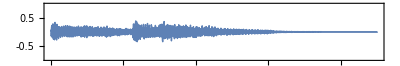

```mathematica
(* 使用AudioPlot来绘制音频文件的响度波形 *)
AudioPlot[%]
```

```mathematica
(* 提取音频文件的数据 *)
data5 = Import["ExampleData/rule30.wav","Data"]
```

```mathematica
Dimensions[data5]
```

{1,79380}

```mathematica
data6 = Import["ExampleData/ocelot.jpg","Data"](* 以矩阵的形式得到图像数据 *)
```

```mathematica
Dimensions[data6]
```

{200,200}

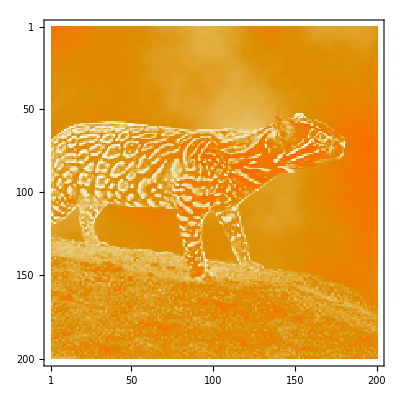

```mathematica
(* 根据矩阵数据绘制图片 *)
MatrixPlot[data6]
```

```mathematica
(* 导入本地文件 *)
Import["C:\\Users\\20613\\Desktop\\CS.png"]
```

-Graphics-

```mathematica
Directory[] (* 说明当前的目录 *)
```

C:\Users\20613\Documents

```mathematica
(* 从网页中导入文件 *)
data7 = Import["https://www.handsonstart.com/ExampleDataSources.txt"]  (* 这是一个具有82个字符的字符串 *)
```

<!DOCTYPE HTML PUBLIC "-//IETF//DTD HTML 2.0//EN">
<html><head>
<title>404 Not Found</title>
</head><body>
<h1>Not Found</h1>
<p>The requested URL was not found on this server.</p>
<p>Additionally, a 404 Not Found
error was encountered while trying to use an ErrorDocument to handle the request.</p>
</body></html>

```mathematica
Dimensions[data7]
```

{}

```mathematica
StringLength[data7]
```

314

```mathematica
(* 使用SematicImport *)
data9 = Import["ExampleData/50states.txt","Data"]
```

{Alabama,Alaska,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Hawaii,Idaho,Illinois,Indiana,Iowa,Kansas,Kentucky,Louisiana,Maine,Maryland,Massachusetts,Michigan,Minnesota,Mississippi,Missouri,Montana,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oklahoma,Oregon,Pennsylvania,Rhode Island,South Carolina,South Dakota,Tennessee,Texas,Utah,Vermont,Virginia,Washington,West Virginia,Wisconsin,Wyoming}

```mathematica
Import["ExampleData/50states.txt"]
```

Alabama
Alaska
Arizona
Arkansas
California
Colorado
Connecticut
Delaware
Florida
Georgia
Hawaii
Idaho
Illinois
Indiana
Iowa
Kansas
Kentucky
Louisiana
Maine
Maryland
Massachusetts
Michigan
Minnesota
Mississippi
Missouri
Montana
Nebraska
Nevada
New Hampshire
New Jersey
New Mexico
New York
North Carolina
North Dakota
Ohio
Oklahoma
Oregon
Pennsylvania
Rhode Island
South Carolina
South Dakota
Tennessee
Texas
Utah
Vermont
Virginia
Washington
West Virginia
Wisconsin
Wyoming

```mathematica
First[data9]
```

Alabama

```mathematica
(* SematicImport *)
data10  = SemanticImport["ExampleData/50states.txt"];
```

```mathematica
First[data10]
```

Alabama, United States

```mathematica
AdministrativeDivisionData[Entity["AdministrativeDivision",{"Alabama","UnitedStates"}],"BorderingStates"]
```

{Florida, United States,Georgia, United States,Mississippi, United States,Tennessee, United States}

```mathematica
(* 从Mathematica中导出数据 *)
(* 查看可以导出的数据格式类型 *)
$ExportFormats
```

{3DS,ACO,AIFF,AU,AVI,Base64,Binary,Bit,BMP,BSON,Byte,BYU,BZIP2,C,CDF,CDXML,Character16,Character32,Character8,CML,Complex128,Complex256,Complex64,CSV,Cube,CUR,DAE,DICOM,DIF,DIMACS,DOT,DTA,DXF,EPS,ExpressionJSON,ExpressionML,FASTA,FASTQ,FBX,FCS,FITS,FLAC,FLV,FMU,GeoJSON,GIF,Graph6,Graphlet,GraphML,GXL,GZIP,HarwellBoeing,HDF,HDF5,HIN,HTML,HTMLFragment,HTTPRequest,HTTPResponse,ICNS,ICO,Ini,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,ISO,JavaProperties,JavaScriptExpression,JPEG,JPEG2000,JSON,JSONLD,JVX,KML,LEDA,List,LWO,MAT,MathML,Matroska,Maya,MCTT,MGF,MIDI,MO,MOL,MOL2,MP3,MP4,MTX,MX,MXNet,NASACDF,NB,NetCDF,NEXUS,NOFF,NQuads,NTriples,OBJ,OFF,Ogg,ONNX,OpenEXR,OWLFunctional,Pajek,PBM,PCX,PDB,PDF,PGM,PHPIni,PLY,PNG,PNM,POR,POV,PPM,PXR,PythonExpression,QuickTime,RawBitmap,RawJSON,RDFXML,Real128,Real32,Real64,RIB,RLE,RTF,SAS7BDAT,SAV,SCT,SDF,SMA,SMILES,SND,SPARQLQuery,SPARQLResultsJSON,SPARQLResultsXML,SPARQLUpdate,Sparse6,STL,String,SurferGrid,SVG,Table,TAR,TerminatedString,TeX,TeXFragment,Text,TGA,TGF,TIFF,TriG,TSV,Turtle,UBJSON,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,UUE,VideoFrames,VRML,VTK,WAV,Wave64,WDX,WebP,WL,WLNet,WMLF,WXF,X3D,XBM,XHTML,XHTMLMathML,XLS,XLSX,XML,XPORT,XYZ,ZIP,ZPR,ZSTD}

```mathematica
(* 导出数字列表 *)
```

```mathematica
data11 = ({{3π, 1/7, 5}, {4.5, 4.75, 4.875}, {ⅇ, 5!, N[π,10]}});
Export["myExportedFile.xlsx",data11]
```

myExportedFile.xlsx

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["myExportedFile.xlsx"]]]
```

```mathematica
Import["myExportedFile.xlsx",data11]
```

{C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx,C:\Users\20613\Documents\myExportedFile.xlsx}

```mathematica
Import["myExportedFile.xlsx"]
```

{{{9.42478,0.142857,5.},{4.5,4.75,4.875},{2.71828,120.,3.14159}}}

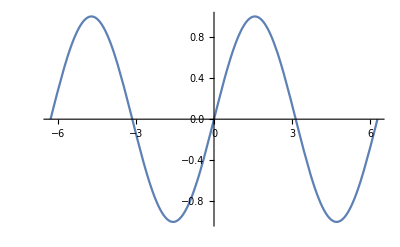

```mathematica
(* 将图形作为图像导出 *)
Plot[Sin[x],{x,-2π,2π}]
```

```mathematica
Export["Sin[x].png",Plot[Sin[x],{x,-2π,2π}]]
```

Sin[x].png

```mathematica
SystemOpen["Sin[x].png"]
```

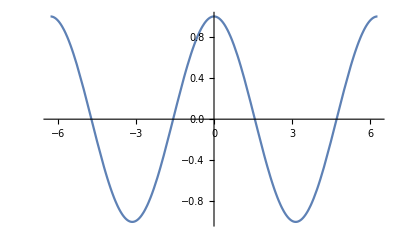

```mathematica
Plot[Cos[x],{x,-2π,2π}]
```

```mathematica
Export["Cos[x].png",-Graphics-]
```

Cos[x].png

```mathematica
SystemOpen["Cos[x].png"]
```

```mathematica
myplot = Plot[Sin[x],{x,-2π,2π}];
Export["data12-C.png",myplot]
```

data12-C.png

```mathematica
SystemOpen["data12-C.png"]
```

```mathematica
(* 通过制定ImageSize参数来获取导出后的更大图像 *)
Export["Cos[x].png",-Graphics-,ImageSize->800]
```

Cos[x].png

```mathematica
SystemOpen["Cos[x].png"]
```

```mathematica
Export["data12-D.png",Plot[Sin[x],{x,-2π,2π}],ImageSize->800]
```

data12-D.png

```mathematica
Export["data12-E.png",Plot[Sin[x],{x,-3π,3π}],ImageSize->800,ImageResolution->300] (* 手动制定图像导出后的分辨率 *)
```

data12-E.png

```mathematica
SystemOpen["data12-E.png"]
```

```mathematica
(* 为3D打印导出图形 *)
ExampleData["Geometry3D"]
```

{{Geometry3D,BassGuitar},{Geometry3D,Beethoven},{Geometry3D,CastleWall},{Geometry3D,Cone},{Geometry3D,Cow},{Geometry3D,Deimos},{Geometry3D,Galleon},{Geometry3D,HammerheadShark},{Geometry3D,Horse},{Geometry3D,KleinBottle},{Geometry3D,MoebiusStrip},{Geometry3D,Phobos},{Geometry3D,PottedPlant},{Geometry3D,Seashell},{Geometry3D,SedanCar},{Geometry3D,SpaceShuttle},{Geometry3D,StanfordBunny},{Geometry3D,Torus},{Geometry3D,Tree},{Geometry3D,Triceratops},{Geometry3D,Tugboat},{Geometry3D,UtahTeapot},{Geometry3D,UtahVWBug},{Geometry3D,Vase},{Geometry3D,VikingLander},{Geometry3D,Wrench},{Geometry3D,Zeppelin}}

```mathematica
Zeppelin = ExampleData[{"Geometry3D","Zeppelin"}]
```

-Graphics3D-

```mathematica
(* 得到针对打印机优化的数据 *)
Printout3D[Zeppelin]
```

```mathematica
Clear[data,data2,data3,data4,data5,data6,data7,data8,data9,data10,data11,myplot,Zeppelin]
```